### Intro

In this notebook I am looking at the size of the response in terms of absolute amplitude.
What this means is that I am looking at a segment of the laser and nerve response for a given animal, and then

### Method 1: [disfavoured] Using the power spectra of the response as the metric

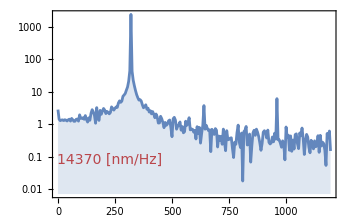

```mathematica
ListLinePlot[fourier[pLaser[[23,5]],sRate,1200],ScalingFunctions->"Log",Filling->Bottom,Epilog->{Inset[Style[ToString[Round[Integrate[Interpolation[fourier[pLaser[[23,5]],sRate,1200]][x],{x,1,1190}],10]]<>" [nm/Hz]",14,red],Scaled[{0.2,0.2}]]}]
```

```mathematica
scaleL=10^-3;(* scaling the laser data to μm rather than nanometers*)
pL=Table[{freqs1T[[i]],j,scaleL Integrate[Interpolation[fourier[pLaser[[i,j]],sRate,1200]][x],{x,1,1190}]},{j,Round[Length@pLaser[[1]]/2]},{i,Length@freqs1T}];
pN=Table[{freqs1T[[i]],j,Integrate[Interpolation[fourier[pNerv[[i,j]],sRate,1200]][x],{x,1,1190}]},{j,Round[Length@pNerv[[1]]/2]},{i,Length@freqs1T}];
```

```mathematica
Grid[{Style[#,18]&/@{"Laser","Nerve"},MapThread[ListLinePlot3D[#1,Filling->Bottom,PlotRange->Full,ImageSize->400,AxesLabel->{"Frequency [Hz]","Segment No",#2}]&,{{pL,pN},{"μm/Hz","mV/Hz"}}]}]
```

Laser | Nerve
-Graphics3D- | -Graphics3D-

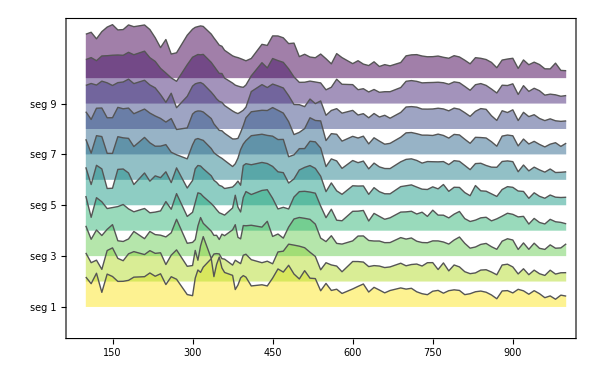
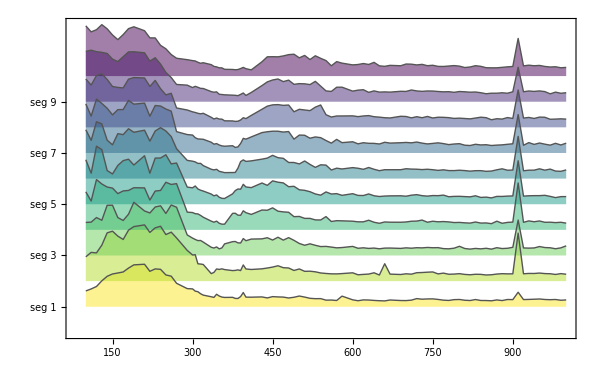

```mathematica
len=Length@freqs;
stepsL=Range[Length@pL]10;
stepsN=Range[Length@pN]10;
imgpadding={{50,50},{50,0}};
viridisCols=Reverse[ColorData["Viridis"][#]&/@Array[1.#&,Length@pL,{0,1}]];
{ListLinePlot[Table[MapAt[#+stepsL[[i]]&,pL[[i,;;,{1,3}]],{All,2}],{i,Length@pL}],PlotStyle->Directive[AbsoluteThickness[1],Darker@Gray],
Filling->{#->{stepsL[[#]],Directive@{Opacity[0.5],viridisCols[[#]]}}&/@Range[Length@pL]},PlotRange->Full,FrameTicks->{Automatic,{stepsL,Style[#,Darker@Gray,12]&/@Table["seg "<>ToString[i],{i,10}]}ᵀ},FrameStyle->{{White,Black},14},ImageSize->600,ImagePadding->imgpadding],

ListLinePlot[Table[MapAt[#+stepsN[[i]]&,pN[[i,;;,{1,3}]],{All,2}],{i,Length@pN}],PlotStyle->Directive[AbsoluteThickness[1],Darker@Gray],
Filling->{#->{stepsN[[#]],Directive@{Opacity[0.5],viridisCols[[#]]}}&/@Range[Length@pN]},PlotRange->Full,FrameTicks->{Automatic,{stepsN,Style[#,Darker@Gray,12]&/@Table["seg "<>ToString[i],{i,10}]}ᵀ},FrameStyle->{{White,Black},14},ImageSize->600,ImagePadding->imgpadding]}
```

```mathematica
Manipulate[ListLinePlot[{pL[[i,;;,{1,3}]],pN[[i,;;,{1,3}]]},AspectRatio->0.5,ImageSize->500,MultiaxisArrangement->{Left->{1,2}},AxesLabel->{"A","B"},PlotLegends->{"laser","nerve"},PlotStyle->{red,green}],{i,1,Length@pL,1},Paneled->False]
```

Part::partd: Part specification pL⟦1,1;;All,{1,3}⟧ is longer than depth of object.

Part::partd: Part specification pN⟦1,1;;All,{1,3}⟧ is longer than depth of object.

Part::partd: Part specification pL⟦1,1;;All,{1,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification pL⟦1,1;;All,{1,3}⟧ is longer than depth of object.

Part::partd: Part specification pN⟦1,1;;All,{1,3}⟧ is longer than depth of object.

Part::partd: Part specification pL⟦1,1;;All,{1,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification pL⟦1,1;;All,{1,3}⟧ is longer than depth of object.

Part::partd: Part specification pN⟦1,1;;All,{1,3}⟧ is longer than depth of object.

Part::partd: Part specification pL⟦1,1;;All,{1,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

### Method 2: Using the envelope of the response as the metric

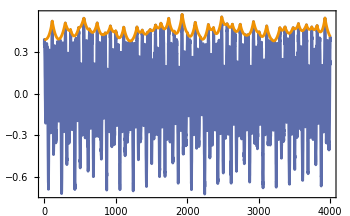

```mathematica
ListLinePlot[{pNerv[[23,5]],-EstimatedBackground[-pNerv[[23,5]],30,Method->{"SNIP",0}]}]
```

```mathematica
scaleL=10^-3; (* factor for scaling the laser data *)
envL=Table[{freqs[[i]],j,scaleL Mean[-EstimatedBackground[-pLaser[[i,j]],30,Method->{"SNIP",0}]]},{j,Round[Length@pLaser[[1]]/2]},{i,Length@freqs}];
envN=Table[{freqs[[i]],j,Mean[-EstimatedBackground[-pNerv[[i,j]],30,Method->{"SNIP",0}]]},{j,Round[Length@pNerv[[1]]/2]},{i,Length@freqs}];
```

```mathematica
Grid[{Style[#,18]&/@{"Laser","Nerve"},MapThread[ListLinePlot3D[#1,Filling->Bottom,PlotRange->#3,
ImageSize->400,AxesLabel->{"Frequency [Hz]","Segment No",#2},
PlotStyle->Directive@{If[tone==1,green,pink],AbsoluteThickness[1]}]&,{{envL,envN},{"μm","mV"},{Full,Full}}]}]
Export[dir<>"\\0_overview\\"<>baseKey<>"_"<>tones[[tone]]<>" overview_3D.png",%,ImageResolution->200];
```

Laser | Nerve
-Graphics3D- | -Graphics3D-

```mathematica
ResourceFunction["AddMatplotlibColors"][]
```

{Magma,Inferno,Plasma,Viridis,EricsRdBuGnYl,EricsRdBuGnYl2,EricsPuBuGnYl,FakeParula,JoesBluGrnPnk2}

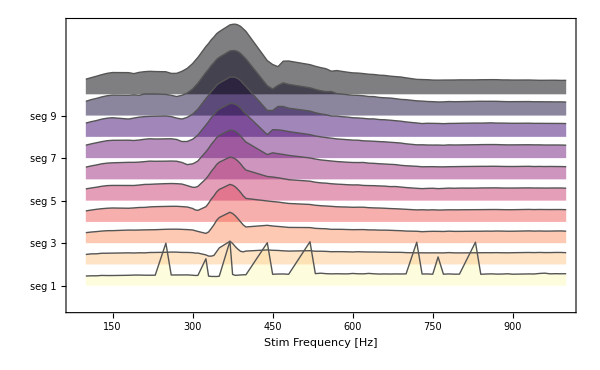
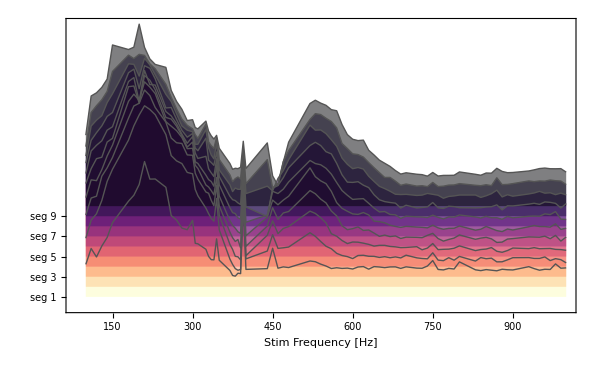
Laser 1T | Nerve 1T
-Graphics- | -Graphics-

```mathematica
len=Length@freqs;
stepsL=Range[Length@envL]If[tone==1,1,3];
stepsN=Range[Length@envN]If[tone==1,0.05,0.2];
imgpadding={{50,50},{50,0}};
overviewCols=Reverse[ColorData["Magma"][#]&/@Array[1.#&,Length@envL,{0,1}]];

Grid[{Style[#,18]&/@{"Laser "<>tones[[tone]],"Nerve "<>tones[[tone]]},{ListLinePlot[Table[MapAt[#+stepsL[[i]]&,envL[[i,;;,{1,3}]],{All,2}],{i,Length@envL}],PlotStyle->Directive[AbsoluteThickness[1],Darker@Gray],
Filling->{#->{stepsL[[#]],Directive@{Opacity[0.5],overviewCols[[#]]}}&/@Range[Length@envL]},PlotRange->Full,FrameTicks->{Automatic,{stepsL,Style[#,Darker@Gray,12]&/@Table["seg "<>ToString[i],{i,10}]}ᵀ},FrameLabel->{"Stim Frequency [Hz]",None},FrameStyle->{{White,Black},14},ImageSize->600,ImagePadding->imgpadding],

ListLinePlot[Table[MapAt[#+stepsN[[i]]&,envN[[i,;;,{1,3}]],{All,2}],{i,Length@envN}],PlotStyle->Directive[AbsoluteThickness[1],Darker@Gray],
Filling->{#->{stepsN[[#]],Directive@{Opacity[0.5],overviewCols[[#]]}}&/@Range[Length@envN]},PlotRange->Full,FrameTicks->{Automatic,{stepsN,Style[#,Darker@Gray,12]&/@Table["seg "<>ToString[i],{i,10}]}ᵀ},FrameLabel->{"Stim Frequency [Hz]",None},FrameStyle->{{White,Black},14},ImageSize->600,ImagePadding->imgpadding]}}]
Export[dir<>"\\0_overview\\M_AGA_Kisumu_ZT11_2023-02-14_No 001_"<>tones[[tone]]<>" overview_stacked2D.png",%,ImageResolution->200];
```

#### Exporting

```mathematica
Export[dir<>"\\0_overview\\"<>baseKey<>"_Laser and Nerve_overview_"<>tones[[tone]]<>".txt",ExportString[<|"laser"->envL,"nerve"->envN|>,"RawJSON","Compact"-> False]]
```

N:\Storage Files\UCL Data\Anopheles\Mosquito 17\set_1\0_overview\M_AGA_G3_ZT14_2025-08-22_No 001_Laser and Nerve_overview_1T.txt

#### Importing

```mathematica
ov1T=Import[FileNames["*_overview_1T"<>"*.txt",dir,∞][[1]],"RawJSON"];(*overview file of the 1T experiments *)
ov2T=Import[FileNames["*_overview_2T"<>"*.txt",dir,∞][[1]],"RawJSON"];(*overview file of the 2T experiments *)
```

```mathematica
Manipulate[MapThread[ListLinePlot[{#1["laser"][[i,;;,{1,3}]],#1["nerve"][[i,;;,{1,3}]]},AspectRatio->0.5,ImageSize->500,MultiaxisArrangement->{Left->{1,2}},AxesLabel->{"A","B"},PlotStyle->#2]&,{{ov1T,ov2T},{{red,green},{blue,orange}}}],{i,1,Length@ov1T["laser"],1},Paneled->False]
```

```mathematica
Clear[axisSizeCalc,rmOut]

(* we want to be able to create an axis bar whose size is about HALF the entire size of the axis. The width of the axis must convey information that is related to the 
actual data. To do this, we find the difference between the min and max of the data and multiply by the size of the AxisObject RELATIVE to the full size of the FULL axis.*)
axisSizeCalc[data_]:=(*ToString@Round[0.5 Max[data]axisSizeD,0.01]*)ToString@Round[Differences@MinMax[data]axisSizeD,0.01][[1]];

(* this is simply to remove data that lie more than σthres away from the mean of the data*)
rmOut[data_,σthres_:4]:=Block[{μ,σ},
{μ,σ}=#[data[[;;,3]]]&/@{Mean,StandardDeviation};
Select[data,Between[#[[3]],μ+σthres{σ,-σ}]&]]

(*ListLinePlot[{ov2T["nerve"][[5]][[;;,{1,3}]],
rmOut[ov2T["nerve"][[5]]][[;;,{1,3}]]}]*)
```

```mathematica
txtSize=12;
axisSize={0.25,0.75};
axisSizeD=Differences[axisSize][[1]];
axisYPos=0.5;
opts={ImageSize->400,ImagePadding->{{100,0},{40,20}},AspectRatio->.5,PlotRange->Full};
{yColL,yColN}={ColorData[97,1],ColorData[97,3]};
{yColL2,yColN2}={ColorData[97,4],ColorData[97,5]};

i=5;
Grid[{Style[#<>" envelope",14]&/@{"one-tone","two-tone"},{Show[{Graphics[{
(* laser/nerve/freq axes *)
AxisObject[{"Vertical",-80,axisSize},BaseStyle->{AbsoluteThickness[2],txtSize,yColL},TickDirection->"Inward",TickPositions->{{axisSize}}
,TickLabels->None,AxisLabel->Placed[axisSizeCalc[ov1T["laser"][[i,;;,3]]]<>" μm",{axisYPos,{0.5,-0.5}}],RotateLabel->90°],
AxisObject[{"Vertical",20,axisSize},BaseStyle->{AbsoluteThickness[2],txtSize,yColN},TickDirection->"Inward",TickPositions->{{axisSize}}
,TickLabels->None,AxisLabel->Placed[axisSizeCalc[ov1T["nerve"][[i,;;,3]]]<>" mV",{axisYPos,{0.5,-0.5}}],RotateLabel->90°],
AxisObject[{"Horizontal",0,{100,1000}},BaseStyle->{AbsoluteThickness[2],txtSize,Gray}]},PlotRange->{{50,1050},{0,1}},opts],
(* laser/nerve data *)
MapThread[ListLinePlot[{#1[[i,;;,1]],#1[[i,;;,3]]/Max[#1[[i,;;,3]]]}ᵀ,Frame->False,Axes->False,PlotStyle->{#2,AbsoluteThickness[2]},opts,Filling->Bottom,FillingStyle->{Opacity[.2]}]&,{{rmOut/@ov1T["laser"],rmOut/@ov1T["nerve"]},{yColL,yColN}}],
Graphics[Inset[LineLegend[{yColL,yColN},Style[#,14]&/@{"laser","nerve"}],Scaled[{0.7,0.9}]]]
}],

Show[{Graphics[{
(* laser/nerve/freq axes *)
AxisObject[{"Vertical",-80,axisSize},BaseStyle->{AbsoluteThickness[2],txtSize,yColL2},TickDirection->"Inward",TickPositions->{{axisSize}}
,TickLabels->None,AxisLabel->Placed[axisSizeCalc[rmOut[ov2T["laser"][[i]]][[;;,3]]]<>" μm",{axisYPos,{0.5,-0.5}}],RotateLabel->90°],
AxisObject[{"Vertical",20,axisSize},BaseStyle->{AbsoluteThickness[2],txtSize,yColN2},TickDirection->"Inward",TickPositions->{{axisSize}}
,TickLabels->None,AxisLabel->Placed[axisSizeCalc[rmOut[ov2T["nerve"][[i]]][[;;,3]]]<>" mV",{axisYPos,{0.5,-0.5}}],RotateLabel->90°],
AxisObject[{"Horizontal",0,{100,1000}},BaseStyle->{AbsoluteThickness[2],txtSize,Gray}]},PlotRange->{{50,1050},{0,1}},opts],
(* laser/nerve data *)
MapThread[ListLinePlot[{#1[[i,;;,1]],#1[[i,;;,3]]/Max[#1[[i,;;,3]]]}ᵀ,Frame->False,Axes->False,PlotStyle->{#2,AbsoluteThickness[2]},opts,Filling->0,FillingStyle->{Opacity[.2]},Epilog->{Inset[Black,"bla",Scaled[{0.2,0.2}]]}]&,{{rmOut/@ov2T["laser"],rmOut/@ov2T["nerve"]},{yColL2,yColN2}}],
Graphics[Inset[LineLegend[{yColL2,yColN2},Style[#,14]&/@{"laser","nerve"}],Scaled[{0.7,0.9}]]]
}]}}]
Export[dir<>"\\0_overview\\"<>baseKey<>"_Laser and Nerve_overview_seg "<>ToString[i]<>".png",%,ImageResolution->200]
```

one-tone envelope | two-tone envelope
-Graphics- | -Graphics-

N:\Storage Files\UCL Data\Anopheles\Mosquito 17\set_1\0_overview\M_AGA_G3_ZT14_2025-08-22_No 001_Laser and Nerve_overview_seg 5.png

```mathematica
Manipulate[ListLinePlot[{ov1T["nerve"][[i,;;,{1,3}]],ov2T["nerve"][[i,;;,{1,3}]]},PlotRange->{0,0.15},ImageSize->500,PlotStyle->{blue,green}],{i,1,10,1},Paneled->False]
```

## Consolidating envelopes from all mosquitoes

We want to be able to separate the animals based on their average mechanical state: SSO, weak SSO, QUIES.
Although it is true that some animals appear to degrade their SSOs with each subsequent set, you can see that the state is fairly representative, so I am not too concenrned to separate them further.
Ideally, we would separate them based on SSO intensity, which might not be too difficult as the mechanical state is not too dissimilar across one set (as we go from 100-1000 Hz).

### Empirical categorisation into SSO, weak SSO and QUIES

NOTE: Before  you do any analysis here, make sure that you apply the envelope analysis from Method 2 from the above section. This analysis is the backbone of everything that follows.

NOTE: The thresholding values for SSO, wSSO and QUIES have been found empirically by looking at a rough envelope analysis and the behaviour of the system at those rough states as well through a PCA analysis, as shown further down. 

These values are also for mosquitoes within the 20-22°C range!!!

```mathematica
<<AlexTools`ALXTools`

expDir="C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\images\\all figures\\new_series\\";
```

```mathematica
Clear[stateChecker]
stateChecker[val_]:=Block[{freq,amp},
{freq,amp}=Mean[readMyFile[#][[;;,2]]]&/@{fftfreq[[val]],fftamp[[val]]};
If[(*both freq and amp are ok, put in SSO *)
Between[freq,ssoRange]&& amp>=ssoMinAmp,AppendTo[sso,val],
(*if not SSO, check for weak SSO *)
If[Between[freq,ssoRange]&& amp>wssoMinAmp,AppendTo[wsso,val],
(*if neither, put in QUIES *)
AppendTo[quies,val]
](* end of second IF *)
] (* end of major IF *)
](* end of block*)
```

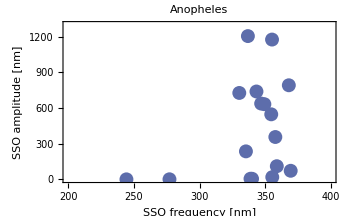
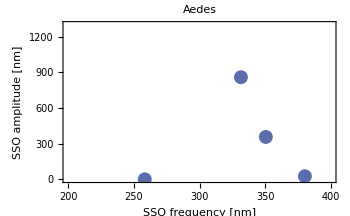
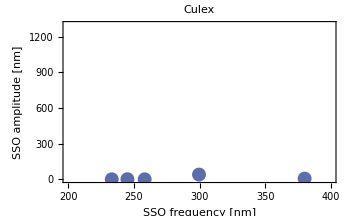

```mathematica
{a,b,c}
```

```mathematica
newSeries = True;
species = 2;
speciesList = {"Aedes","Anopheles","Culex"};
speciesCorrespondence = <|"Aedes"->"AAE","Anopheles"->"AGA","Culex"->"CQU"|>;
thisDir = If[newSeries,"N:\\Storage Files\\UCL Data\\"<>speciesList[[species]]<>"\\","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\"];
(*SetDirectory["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito25\\set_1"];*)

dir = SetDirectory[thisDir]
fftfreq=Select[FileNames["*0_FFT_freqs_*",thisDir,4],StringContainsQ[#,"set_"]&]; (* find all the prestim frequencies of mosquitoes*)
fftamp=Select[FileNames["*0_FFT_amplitudes_*",thisDir,4],StringContainsQ[#,"set_"]&]; (* find all the prestim amplitudes of mosquitoes*)

speciesDictionary = <|
"AAE"-><|"minSSOAmp"->20,"ssoRange"->{300,500}|>,
"AGA"-><|"minSSOAmp"->135,"ssoRange"->{300,400}|>,
"CQU"-><|"minSSOAmp"->80,"ssoRange"->{200,400}|>|>;



ssoRange=speciesDictionary[speciesCorrespondence[speciesList[[species]]]]["ssoRange"]; (* Default:{300,500} expected values of SSO frequency*)
ssoMinAmp=speciesDictionary[speciesCorrespondence[speciesList[[species]]]]["minSSOAmp"]; (* Default:200 the minimum amplitude we expect for an SSOing animal*)
wssoMinAmp=1;(* Default:10 the minimum amplitude we expect for a weakly SSOing animal*)

(* previously we would attribute a state based on the mosquito. Here we will attribute a state based on the set, and pool the data together.*)
sso={}; (* animals that meet frequency and amplitude criteria for SSO *)
wsso={}; (* animals that only meet frequency criteria but not the amplitude ones *)
quies={}; (* neither amp nor freq criteria are met *)
stateChecker[#]&/@Range[Length@fftfreq];
{{"SSO","wSSO","QUIES"},Length/@{sso,wsso,quies}}ᵀ//TableForm
sso
wsso
quies
```

N:\Storage Files\UCL Data\Anopheles

SSO | 10
wSSO | 5
QUIES | 2

{1,3,4,5,8,12,13,14,15,16}

{2,6,10,11,17}

{7,9}

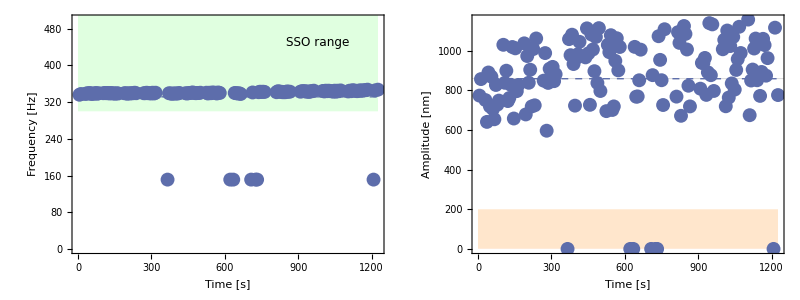

```mathematica
i=4;
Grid@{{ListPlot[readMyFile[fftfreq[[i]]],Prolog->{LightGreen,Rectangle[{0,ssoRange[[1]]},{Max[readMyFile[fftfreq[[i]]][[;;,1]]],1200}]},
Epilog->{Dashed,blue,Line[{{0,Mean[readMyFile[fftfreq[[i]]][[;;,2]]]},{Max[readMyFile[fftfreq[[i]]][[;;,1]]],Mean[readMyFile[fftfreq[[i]]][[;;,2]]]}}],Inset[Style["SSO range",12,Black],{0.8Max[readMyFile[fftfreq[[i]]][[;;,1]]], 450 }]},PlotRange->{0,500},FrameLabel->{"Time [s]","Frequency [Hz]"}],
ListPlot[readMyFile[fftamp[[i]]],GridLines->{None,{Mean[readMyFile[fftamp[[i]]][[;;,2]]]}},
Prolog->{LightRed,Rectangle[{0,0},{Max[readMyFile[fftamp[[i]]][[;;,1]]],wssoMinAmp}],LightOrange,Rectangle[{0,wssoMinAmp},{Max[readMyFile[fftamp[[i]]][[;;,1]]],ssoMinAmp}]},
Epilog->{Dashed,blue,Line[{{0,Mean[readMyFile[fftamp[[i]]][[;;,2]]]},{Max[readMyFile[fftamp[[i]]][[;;,1]]],Mean[readMyFile[fftamp[[i]]][[;;,2]]]}}]},FrameLabel->{"Time [s]","Amplitude [nm]"}]}}
```

### Importing

```mathematica
Clear[getBasePath]
getBasePath[path_String]:=First@StringCases[path,StartOfString~~Shortest[___~~"Mosquito "~~DigitCharacter..~~"\\"~~"set_"~~DigitCharacter..~~"\\"]]
getBasePath2[path_String]:=First@StringCases[path,Shortest["Mosquito "~~DigitCharacter..~~"\\"~~"set_"~~DigitCharacter..~~"\\"]]
(*getBasePath[fftfreq[[2]]]
getBasePath2[fftfreq[[2]]]*)
```

```mathematica
Clear[bringThemIn]
(*---------------------------------------------------------------------------------------------------------------*)
(* NOTE! PLEASE ENABLE THE TOP ONE FOR OLD DATA AND THE BOTTOM ONE FOR NEW DATA! CANT MAKE IT WORK AS ONE UNIFIED FUNCTION*)
(*---------------------------------------------------------------------------------------------------------------*)


(*bringThemIn[tone_,filenames_]:=Block[{fn,vals},
(*tone: "1T" or "2T"
filenames: sso,wsso or quies
*)
fn=FileNames["*_overview_"<>tone<>"*.txt",StringTake[fftfreq[[#]],58],∞]&/@ filenames;
MapThread[If[#2=={},Print["Could not load "<>tone<>" of: "<>StringTake[fftfreq[[#1]],{42,58}]]]&,{filenames,fn}];
vals=DeleteCases[MapThread[StringTake[fftfreq[[#1]],{42,58}]->#2&,{filenames,fn}],_->{}];
AssociationThread[Keys@vals,Import[#[[1]],"RawJSON"]&/@Values[vals]]
]*)


bringThemIn[tone_,filenames_]:=Block[{fn,vals},
(*tone: "1T" or "2T"
filenames: sso,wsso or quies
*)
fn=FileNames["*_overview_"<>tone<>"*.txt",getBasePath[fftfreq[[#]]],∞]&/@ filenames;
MapThread[If[#2=={},Print["Could not load "<>tone<>" of: "<>getBasePath2[fftfreq[[#]]]]]&,{filenames,fn}];
vals=DeleteCases[MapThread[getBasePath2[fftfreq[[#]]]->#2&,{filenames,fn}],_->{}];
AssociationThread[Keys@vals,Import[#[[1]],"RawJSON"]&/@Values[vals]]
]
(*bringThemIn["1T",sso]*)
```

```mathematica
sso1T=bringThemIn["1T",sso];
sso2T=bringThemIn["2T",sso];

wsso1T=bringThemIn["1T",wsso];
wsso2T=bringThemIn["2T",wsso];

quies1T=bringThemIn["1T",quies];
quies2T=bringThemIn["2T",quies];

(* use this if you want to remove the new data *)
(*sso1T=KeyDrop[sso1T,Keys[sso1T][[-4;;]]];
wsso1T=KeyDrop[wsso1T,Keys[wsso1T][[-1;;]]];
sso2T=KeyDrop[sso2T,Keys[sso2T][[-4;;]]];
wsso2T=KeyDrop[wsso2T,Keys[wsso2T][[-1;;]]];*)

(* use this if you want to remove the new data from the 2025 series *)
(*sso1T=KeyDrop[sso1T,Keys[sso1T][[-4;;]]];
wsso1T=KeyDrop[wsso1T,Keys[wsso1T][[-1;;]]];
sso2T=KeyDrop[sso2T,Keys[sso2T][[-4;;]]];
wsso2T=KeyDrop[wsso2T,Keys[wsso2T][[-1;;]]];*)
```

```mathematica
Grid[{{"SSO","weak SSO","QUIES"},Column[Keys[#]]&/@{sso1T,wsso1T,quies1T}},Alignment->Top]
```

SSO | weak SSO | QUIES
Mosquito 10\set_1\
Mosquito 12\set_1\
Mosquito 13\set_1\
Mosquito 14\set_1\
Mosquito 17\set_1\
Mosquito 4\set_1\
Mosquito 5\set_1\
Mosquito 6\set_1\
Mosquito 7\set_1\
Mosquito 8\set_1\ | Mosquito 11\set_1\
Mosquito 15\set_1\
Mosquito 2\set_1\
Mosquito 3\set_1\
Mosquito 9\set_1\ | Mosquito 16\set_1\
Mosquito 1\set_1\

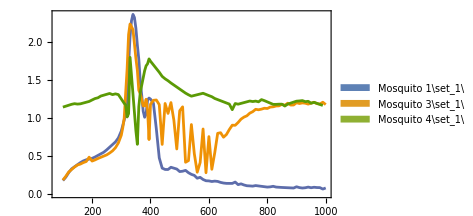
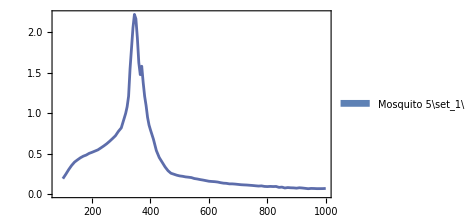
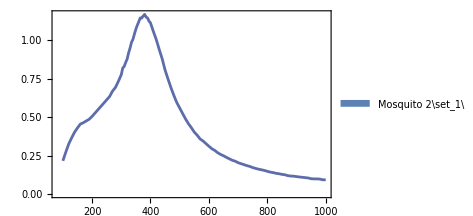
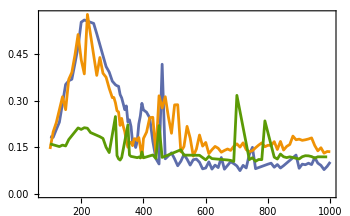
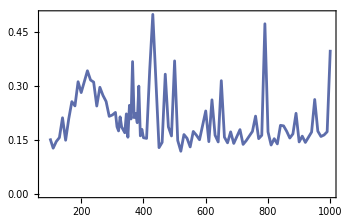
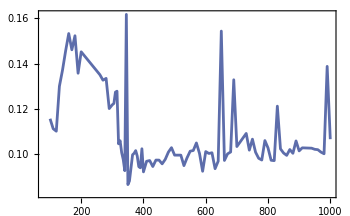
| SSO | weak SSO | QUIES
Laser | -Graphics- | -Graphics- | -Graphics-
Nerve | -Graphics- | -Graphics- | -Graphics-

```mathematica
intensity=5;
Grid@{Style[#,20,pink]&/@{"","SSO","weak SSO","QUIES"},
(*laser data*)
{Style["Laser",20,blue],Splice[Table[ListLinePlot[Values[d][[#]]["laser"][[intensity]][[;;,{1,3}]]&/@Range[Length@d],Epilog->Inset[SwatchLegend[ColorData[97][#]&/@Range[Length@Keys[d]],Keys[d]],Scaled[{0.8,0.8}]]],{d,{sso1T,wsso1T,quies1T}}]]},
(*nerve data*)
{Style["Nerve",20,green],Splice[Table[ListLinePlot[Values[d][[#]]["nerve"][[intensity]][[;;,{1,3}]]&/@Range[Length@d]],{d,{sso1T,wsso1T,quies1T}}]]}}
```

### Baseline removal

```mathematica
Clear[bgRemoval]
bgRemoval[data_,type_,intensity_]:=Block[{raw,raw2,μ,min,max},
If[MissingQ[data[type]],Nothing,
raw=data[type][[intensity]][[;;,{1,3}]];
raw2=Select[raw,Between[#[[2]],Mean[raw[[;;,2]]]+{-1,1}*3StandardDeviation[raw[[;;,2]]]]&];
μ=EstimatedBackground[raw2[[;;,2]],50,Method->{"SNIP",0}];
{min,max}={Mean@μ,Max[Select[raw2,Between[#[[1]],{100,400}]&][[;;,2]]]};
Select[{raw2[[;;,1]],(raw2[[;;,2]]-μ)/(max-min)}ᵀ,1.1 >=#[[2]]>=-0.1&]
]
]
```

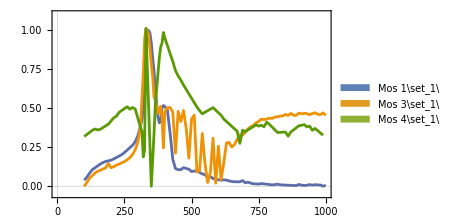
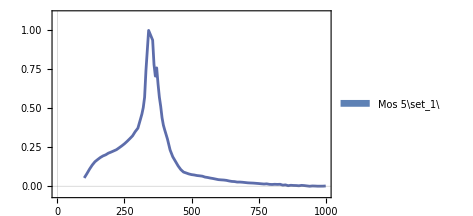
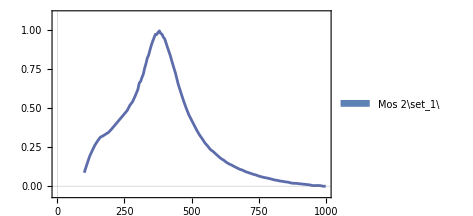
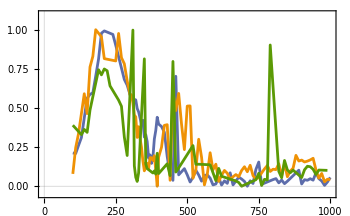
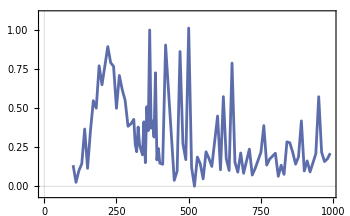
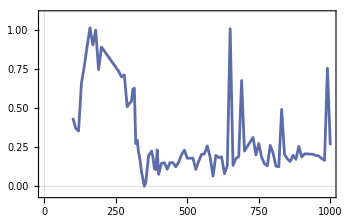
| SSO | weak SSO | QUIES
Laser | -Graphics- | -Graphics- | -Graphics-
Nerve | -Graphics- | -Graphics- | -Graphics-

```mathematica
intensity=5;
Grid[{Style[#,20,pink]&/@{"","SSO","weak SSO","QUIES"},{Style["Laser",20,blue]}~Join~MapThread[ListLinePlot[bgRemoval[#,"laser",intensity]&/@#1,PlotRange->{-0.05,1.1},PlotLegends->None,Epilog->Inset[SwatchLegend[ColorData[97][#]&/@Range[Length@Keys[#1]],StringReplace[Keys[#1],"Mosquito"->"Mos "]],Scaled[{0.8,0.8}]],GridLines->{{0}, {0}}]&,{{sso1T,wsso1T,quies1T}}],
{Style["Nerve",20,green]}~Join~
MapThread[ListLinePlot[bgRemoval[#,"nerve",intensity]&/@#1,PlotRange->{-0.05,1.1},PlotLegends->None,GridLines->{{0}, {0}}]&,{{sso1T,wsso1T,quies1T}}]
}]
```

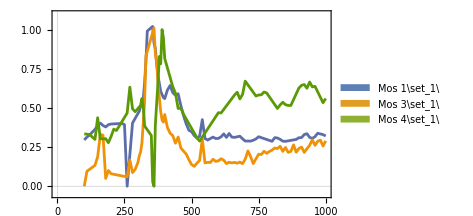
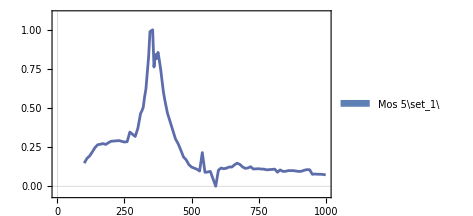
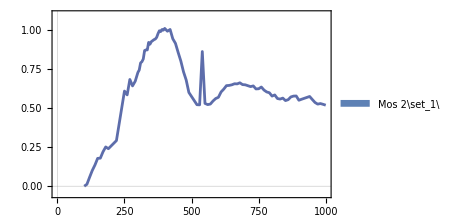
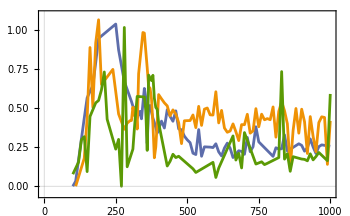
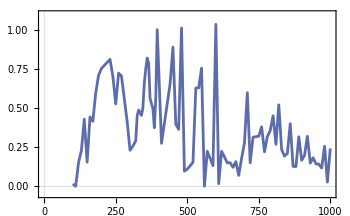
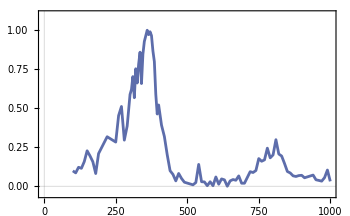
| SSO | weak SSO | QUIES
Laser | -Graphics- | -Graphics- | -Graphics-
Nerve | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{Style[#,20,pink]&/@{"","SSO","weak SSO","QUIES"},{Style["Laser",20,blue]}~Join~MapThread[ListLinePlot[bgRemoval[#,"laser",intensity]&/@#1,PlotRange->{-0.05,1.1},PlotLegends->None,Epilog->Inset[SwatchLegend[ColorData[97][#]&/@Range[Length@Keys[#1]],StringReplace[Keys[#1],"Mosquito"->"Mos "]],Scaled[{0.8,0.8}]],GridLines->{{0}, {0}}]&,{{sso2T,wsso2T,quies2T}}],
{Style["Nerve",20,green]}~Join~
MapThread[ListLinePlot[bgRemoval[#,"nerve",intensity]&/@#1,PlotRange->{-0.05,1.1},PlotLegends->None,GridLines->{{0}, {0}}]&,{{sso2T,wsso2T,quies2T}}]
}]
```

```mathematica
Clear[avgError,bands]
avgError[data_]:=Block[{g,avg,σ},
g=GatherBy[Flatten[data,1],#[[1]]&] (* gather all the elements by frequency *);
avg=Sort[Mean/@g](* find the average and sort the data*);
σ=(If[Length@#<2,{0.001,0.001},StandardDeviation@#]&/@g)[[;;,2]] (*find the standard deviation for each grouping. Return σ=0 for that cell if only one entry*);
{avg[[;;,1]],Around@@#&/@({avg[[;;,2]],σ}ᵀ)}ᵀ (* create the error bars*)
]

bands[data_,σ_:3]:=Block[{},
(*expects the output of the avgError function
σ denotes how many st.deviations away you want to account for *)
{data[[;;,1]],#/.x_/;x<0->0}ᵀ&/@{(#["Value"]+σ#["Uncertainty"]&/@data[[;;,2]]),(#["Value"]-σ#["Uncertainty"]&/@data[[;;,2]])}
]

bands[data_]:=Block[{min,max},
(*alternative to bands. essentially collates all the data and finds the upper and lower bounds of all of them *)
{min,max}=Sort/@Table[{#[[1,1]],func[#[[;;,2]]]}&/@GatherBy[Flatten[data,1],#[[1]]&],{func,{Min,Max}}]
]
```

```mathematica
intensity=5;
envL1T=Values/@MapThread[bgRemoval[#,"laser",intensity]&/@#1&,{{sso1T,wsso1T,quies1T}}]; 
envN1T=Values/@MapThread[bgRemoval[#,"nerve",intensity]&/@#1&,{{sso1T,wsso1T,quies1T}}]; 
envL2T=Values/@MapThread[bgRemoval[#,"laser",intensity]&/@#1&,{{sso2T,wsso2T,quies2T}}]; 
envN2T=Values/@MapThread[bgRemoval[#,"nerve",intensity]&/@#1&,{{sso2T,wsso2T,quies2T}}];
```

```mathematica
expDir
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\all figures\new_series\

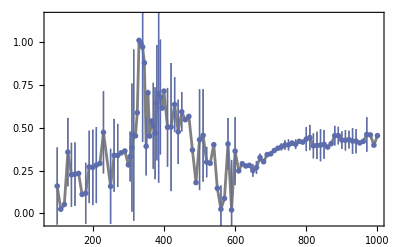
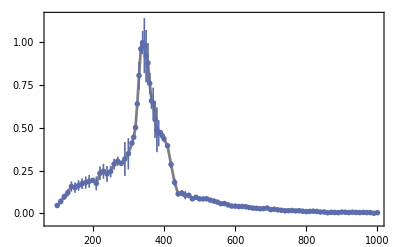
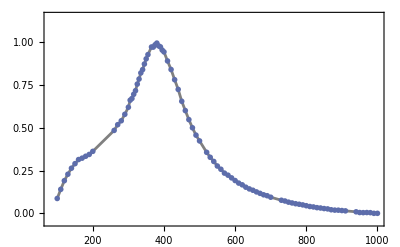
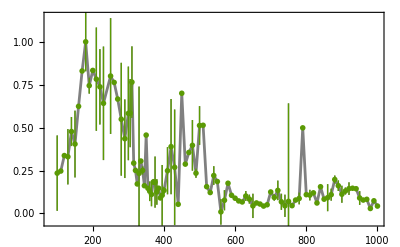
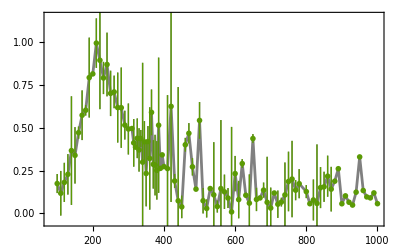
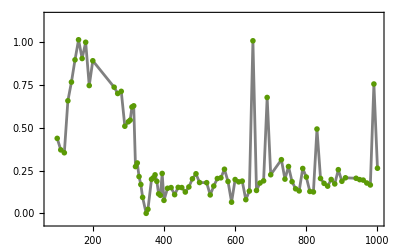
| SSO | weak SSO | QUIES
Laser | -Graphics- | -Graphics- | -Graphics-
Nerve | -Graphics- | -Graphics- | -Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\all figures\new_series\\sensitivity regions of nerve and flagellum\sensitivity region_1T_segment 5XX1.png

```mathematica
opts={PlotStyle->Directive[LightGray],FillingStyle->{Opacity[1]}(*,GridLines->{{100},{0}}*),PlotRange->{Full,{-0.05,1.15}},
FrameStyle->Directive[Lighter@Gray,FontSize->18,AbsoluteThickness[2]]};

Grid[{Style[#,20,Darker@Gray]&/@{"","SSO","weak SSO","QUIES"},
{Style["Laser",20,blue]}~Join~MapThread[Show[{
(*ListLinePlot[bands[#1],Filling->{1->{2}},opts],*)
ListLinePlot[avgError[#1],PlotStyle->{Gray},opts],
ListPlot[avgError[#1],PlotStyle->{blue},PlotMarkers->{"OpenMarkers",6}]},ImageSize->400]&,{envL1T}],
{Style["Nerve",20,green]}~Join~
MapThread[Show[{(*ListLinePlot[bands[#1],Filling->{1->{2}},opts],*)
ListLinePlot[avgError[#1],PlotStyle->{Gray},opts],
ListPlot[avgError[#1],PlotStyle->{green},PlotMarkers->{"OpenMarkers",6}]},ImageSize->400]&,{envN1T}]}]
Export[expDir<>"\\sensitivity regions of nerve and flagellum\\"<>"sensitivity region_1T_segment "<>ToString[intensity]<>"XX1.png",%,ImageResolution->200]
```

```mathematica
11.35/5
```

2.27

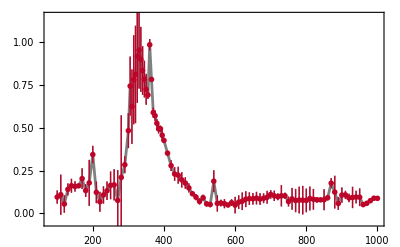
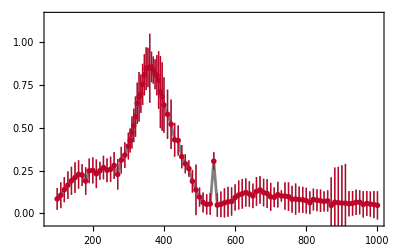
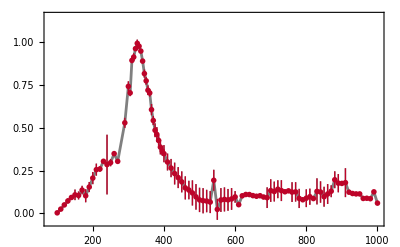
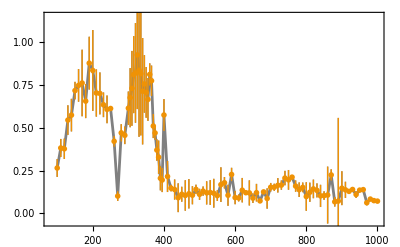
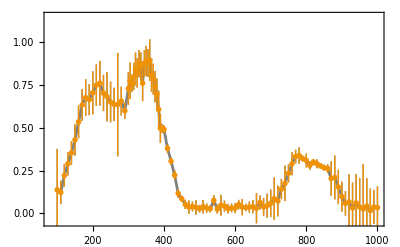
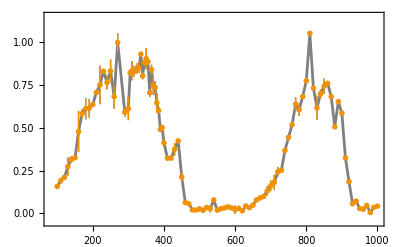
| SSO | weak SSO | QUIES
Laser | -Graphics- | -Graphics- | -Graphics-
Nerve | -Graphics- | -Graphics- | -Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\DP concept paper\images\all figures\sensitivity regions of nerve and flagellum\sensitivity region_2T_segment 5222.png

```mathematica
Grid[{Style[#,20,Darker@Gray]&/@{"","SSO","weak SSO","QUIES"},{Style["Laser",20,red]}~Join~MapThread[Show[{
(*ListLinePlot[#1,PlotStyle->Directive[LightGray],Filling->(1->{#}&/@Range[Length@#1]),opts],*)
ListLinePlot[avgError[#1],PlotStyle->{Gray},opts],
ListPlot[avgError[#1],PlotStyle->{red},PlotMarkers->{"OpenMarkers",6}]},ImageSize->400]&,{envL2T}],
{Style["Nerve",20,orange]}~Join~
MapThread[Show[{(*ListLinePlot[#1(*bands[avgError[#1],2]*),PlotStyle->Directive[LightGray],Filling->(1->{#}&/@Range[Length@#1]),opts],*)
ListLinePlot[avgError[#1],PlotStyle->{Gray},opts],
ListPlot[avgError[#1],PlotStyle->{orange},PlotMarkers->{"OpenMarkers",6}]},ImageSize->400]&,{envN2T}]}]
Export["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\DP concept paper\\images\\all figures\\sensitivity regions of nerve and flagellum\\"<>"sensitivity region_2T_segment "<>ToString[intensity]<>"222.png",%,ImageResolution->200]
```

```mathematica
540-270.
```

270.

#### Creating some nicer figures

```mathematica
intensity=5;
envL1T=Values/@MapThread[bgRemoval[#,"laser",intensity]&/@#1&,{Reverse@{sso1T,wsso1T,quies1T}}]; 
envN1T=Values/@MapThread[bgRemoval[#,"nerve",intensity]&/@#1&,{Reverse@{sso1T,wsso1T,quies1T}}]; 
envL2T=Values/@MapThread[bgRemoval[#,"laser",intensity]&/@#1&,{Reverse@{sso2T,wsso2T,quies2T}}]; 
envN2T=Values/@MapThread[bgRemoval[#,"nerve",intensity]&/@#1&,{Reverse@{sso2T,wsso2T,quies2T}}]; 

{tickSizeMinor,tickSizeMajor}={0.005,0.01};
fticksX={Range[200,1000,200],Range[200,1000,200],{0,tickSizeMajor}&/@Range[5]}ᵀ;
fticksx=Select[Table[{i,"",{0,If[Mod[i,100]==0,tickSizeMajor,tickSizeMinor]}},{i,100,1000,50}],Not@MemberQ[fticksX[[;;,1]],#[[1]]]&];
fticksX=fticksX~Join~fticksx;
fticksY={{0,0.5,1},{0,0.5,1},{0,tickSizeMajor}&/@Range[3]}ᵀ;
```

https://resources.wolframcloud.com/FunctionRepository/resources/PolygonMarker
https://mathematica.stackexchange.com/questions/84857/how-can-we-make-publication-quality-plotmarkers-without-version-10
Use these colour schemes from this website.

```mathematica
Clear[em,fm,fm2]
ResourceFunction["PolygonMarker"];
(* empty marker *)
em[name_String, size_ : 7] := ResourceFunction["PolygonMarker"][name, Offset[size],
   {Dynamic@
     EdgeForm[{CurrentValue["Color"], JoinForm["Round"], AbsoluteThickness[2], Opacity[1]}], FaceForm[White]},
   ImagePadding -> 6];
(*filled marker*)
fm[name_String,size_:8]:=ResourceFunction["PolygonMarker"][name,Offset[size],EdgeForm[]];
(* lightly filled marker *)
fm2[name_String,size_:9,opacity_:0.75]:=ResourceFunction["PolygonMarker"][name,Offset@size,
{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[1]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],opacity]}];

fm3[name_String,size_:9,opacity_:0.75,edgeThickness_:2,edgeOpacity_:1]:=ResourceFunction["PolygonMarker"][name,Offset@size,
{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[edgeOpacity],AbsoluteThickness[edgeThickness]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],opacity]}];

allShapes=ResourceFunction["PolygonMarker"][All]
```

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarSlim,FivePointedStarThick,DancingStar,DancingStarRight,DancingStarThick,DancingStarThickRight,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SixfoldPinwheel,SixfoldPinwheelRight,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,SevenfoldPinwheel,SevenfoldPinwheelRight,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

```mathematica
hexToRGB["#800020"]
RGBColor@@({170,021,041}/255)
```

RGBColor[0.5019607843137255, 0., 0.12549019607843137]

RGBColor[Rational[2, 3], Rational[7, 85], Rational[41, 255]]

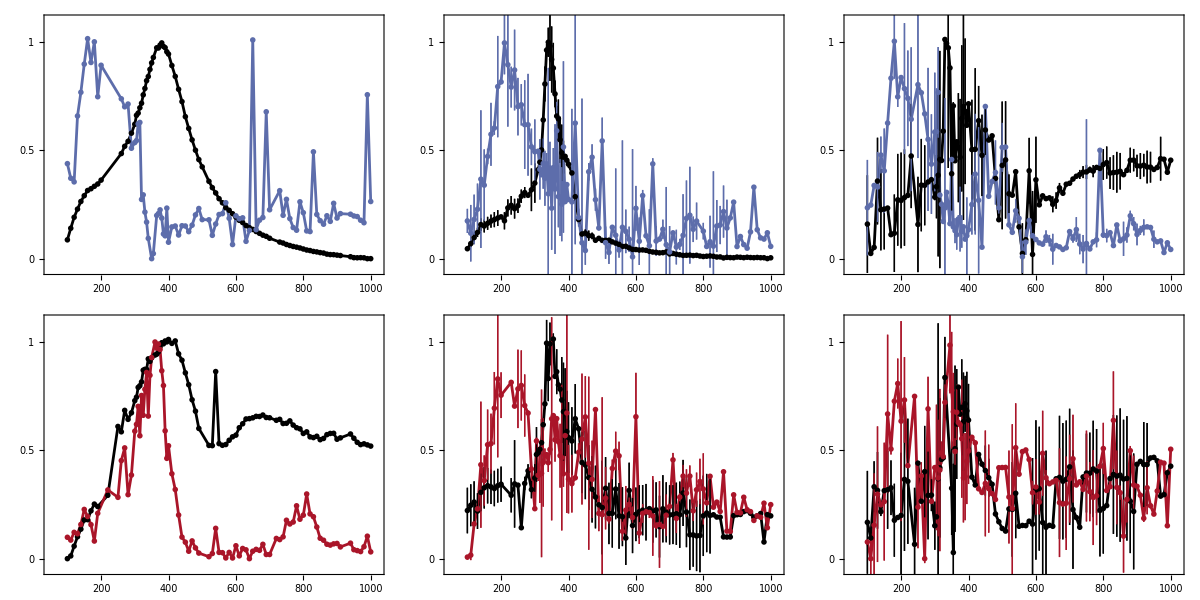

```mathematica
opts={FrameTicks->{fticksX,fticksY},PlotRange->{{50,1020},{-0.05,1.1}},ImageSize->300,FrameStyle->Directive@{Black,AbsoluteThickness[1.5],FontSize->18,FontFamily->"Helvetica"}};

{col1T,col1TN}={Black,blue};
{col2T,col2TN}={Black,(*hexToRGB["#800020"]*)RGBColor@@({170,021,041}/255)};
{circle,uptriangle,diamond,square,downtriangle}=Charting`CommonDump`GraphicsOpenPlotMarkers[][[;;5]];
(*ChartElementData["PlotMarkers"]*)
op=.6;
op2=.4;
size=5;

Grid[{MapThread[
Show[{(*ListLinePlot[bands[envL1T[[#1]]],Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{col1T,Opacity[0.1]},opts],
ListLinePlot[bands[envN1T[[#1]]],Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{col1TN,Opacity[0.2]},opts],*)
ListLinePlot[{avgError[envL1T[[#1]]],avgError[envN1T[[#1]]]},PlotStyle->{{col1T,AbsoluteThickness[2]},{col1TN,AbsoluteThickness[2]}},opts],
ListPlot[{avgError[envL1T[[#1]]],avgError[envN1T[[#1]]]},PlotStyle->{col1T ,col1TN},PlotMarkers->{fm2["Circle",size,op],fm2["UpTriangle",5,op]}(*PlotMarkers->{{Automatic,8},{uptriangle,6}}*)]}]&,{Range[3]}],
MapThread[
Show[{(*ListLinePlot[bands[envL2T[[#1]]],Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{col2T,Opacity[0.1]},opts],
ListLinePlot[bands[envN2T[[#1]]],Filling->{1->{2}},PlotStyle->Opacity[0],FillingStyle->Directive@{col2TN,Opacity[0.2]}],*)
ListLinePlot[{avgError[envL2T[[#1]]],avgError[envN2T[[#1]]]},PlotStyle->{{col2T,AbsoluteThickness[2]},{col2TN,AbsoluteThickness[2]}},opts],
ListPlot[{avgError[envL2T[[#1]]],avgError[envN2T[[#1]]]},PlotStyle->{col2T,col2TN},PlotMarkers->{fm2["Diamond",size,op2],fm2["DownTriangle",5,op]}(*{{Automatic,6},{uptriangle,6}}*)(*PlotMarkers->{"OpenMarkers",6}*)]}]&,{Range[3]}]}]
(*Export["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\DP concept paper\\images\\all figures\\sensitivity regions of nerve and flagellum\\"<>"sensitivity region_combined_segment_v.10_ "<>ToString[intensity]<>".png",%,ImageResolution->200,Background->None]*)
```

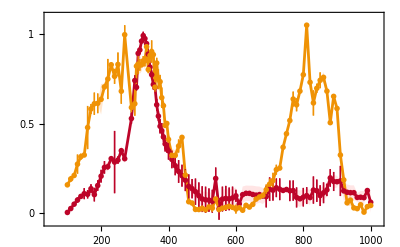

```mathematica
i=1;
Show[{
ListLinePlot[bands[envL2T[[i]]],Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{Red,Opacity[0.1]},FrameTicks->{fticksX,fticksY},PlotRange->{{50,1020},{-0.05,1.1}},ImageSize->400,FrameStyle->Directive@{Darker@Gray,AbsoluteThickness[1.5],FontSize->18}],
ListLinePlot[bands[envN2T[[i]]],Filling->{1->{2}},PlotStyle->Opacity[0],FillingStyle->Directive@{Orange,Opacity[0.2]}],
ListLinePlot[{avgError[envL2T[[i]]],avgError[envN2T[[i]]]},PlotStyle->{{red,AbsoluteThickness[2]},{orange,AbsoluteThickness[2]}}],
ListPlot[{avgError[envL2T[[i]]],avgError[envN2T[[i]]]},PlotStyle->{red,orange},PlotMarkers->{"OpenMarkers",6}]}]
```

### Publication figures

#### Nicer figures but grouping the analysis by animal.

Here we first take the average of EACH animal, and then pool them together.
This means that we will yield:
QUIES: N=1
wSSO: N=6
SSO: N=3

```mathematica
Length/@{sso1TG,wSSO1TG,quies1TG}
Length/@{sso2TG,wSSO2TG,quies2TG}
```

{0,4,2}

{0,4,2}

```mathematica
{tickSizeMinor,tickSizeMajor}={0.005,0.01};
fticksX={Range[200,1000,200],Range[200,1000,200],{0,tickSizeMajor}&/@Range[5]}ᵀ;
fticksx=Select[Table[{i,"",{0,If[Mod[i,100]==0,tickSizeMajor,tickSizeMinor]}},{i,100,1000,50}],Not@MemberQ[fticksX[[;;,1]],#[[1]]]&];
fticksX=fticksX~Join~fticksx;
fticksY={{0,0.5,1},{0,0.5,1},{0,tickSizeMajor}&/@Range[3]}ᵀ;


opts={FrameTicks->{fticksX,fticksY},PlotRange->{{50,1020},{-0.05,1.1}},ImageSize->300,FrameStyle->Directive@{Black,AbsoluteThickness[1.5],FontSize->18,FontFamily->"Helvetica"}};

{col1T,col1TN}={Black,blue};
{col2T,col2TN}={Black,(*hexToRGB["#800020"]*)RGBColor@@({170,021,041}/255)};
{circle,uptriangle,diamond,square,downtriangle}=Charting`CommonDump`GraphicsOpenPlotMarkers[][[;;5]];
(*ChartElementData["PlotMarkers"]*)
op=.6;
op2=.4;
size=5;

sso1TG=Normal[Dataset[<|Table[Keys[sso1T][[i]]->Append[sso1T[[Keys[sso1T][[i]]]],"mos_ID"->StringSplit[Keys[sso1T][[i]],"\\"][[1]]],{i,Length@sso1T}]|>][GroupBy["mos_ID"]]];
wSSO1TG=Normal[Dataset[<|Table[Keys[wsso1T][[i]]->Append[wsso1T[[Keys[wsso1T][[i]]]],"mos_ID"->StringSplit[Keys[wsso1T][[i]],"\\"][[1]]],{i,Length@wsso1T}]|>][GroupBy["mos_ID"]]];
quies1TG=Normal[Dataset[<|Table[Keys[quies1T][[i]]->Append[quies1T[[Keys[quies1T][[i]]]],"mos_ID"->StringSplit[Keys[quies1T][[i]],"\\"][[1]]],{i,Length@quies1T}]|>][GroupBy["mos_ID"]]];

sso2TG=Normal[Dataset[<|Table[Keys[sso2T][[i]]->Append[sso2T[[Keys[sso2T][[i]]]],"mos_ID"->StringSplit[Keys[sso2T][[i]],"\\"][[1]]],{i,Length@sso2T}]|>][GroupBy["mos_ID"]]];
wSSO2TG=Normal[Dataset[<|Table[Keys[wsso2T][[i]]->Append[wsso2T[[Keys[wsso2T][[i]]]],"mos_ID"->StringSplit[Keys[wsso2T][[i]],"\\"][[1]]],{i,Length@wsso2T}]|>][GroupBy["mos_ID"]]];
quies2TG=Normal[Dataset[<|Table[Keys[quies2T][[i]]->Append[quies2T[[Keys[quies2T][[i]]]],"mos_ID"->StringSplit[Keys[quies2T][[i]],"\\"][[1]]],{i,Length@quies2T}]|>][GroupBy["mos_ID"]]];
```

```mathematica
If[newSeries && species ==2,
quies1TG  = KeyDrop[quies1TG,"Mosquito 16"]; (* remove Mosquito 16 from the 1T data*)
quies2TG  = KeyDrop[quies2TG,"Mosquito 16"]; (* remove Mosquito 16 from the 2T data*)
wSSO2TG  = KeyDrop[wSSO2TG,"Mosquito 2"];     (* remove Mosquito 2 from the 2T data*)
]
If[newSeries && species ==3,
quies1TG = KeyDrop[quies1TG,"Mosquito 3"];
quies2TG = KeyDrop[quies2TG,"Mosquito 3"];]
```

```mathematica
(*DO NOT DELETE THESE. THEY ARE USED FOR COMBINING THE OLD AND NEW ANOPHELES DATASETS*)
```

```mathematica
(*{newquies1T,newwsso1T,newsso1T}={quies1TG,wSSO1TG,sso1TG};
{newquies2T,newwsso2T,newsso2T}={quies2TG,wSSO2TG,sso2TG};*)
```

```mathematica
(*{oldquies1T,oldwsso1T,oldsso1T}={quies1TG,wSSO1TG,sso1TG};
{oldquies2T,oldwsso2T,oldsso2T}={quies2TG,wSSO2TG,sso2TG};*)
```

```mathematica
(*quies1TG = <|oldquies1T,newquies1T|>;
quies2TG = <|oldquies2T,newquies2T|>;
wSSO1TG = <|oldwsso1T,newwsso1T|>;
wSSO2TG = <|newwsso2T,newwsso2T|>;
sso1TG = <|oldsso1T,newsso1T|>;
sso2TG = <|newsso2T,newsso2T|>;*)
```

```mathematica
intensity=5;

Clear[groupExtractor]
groupExtractor[data_,channel_:"laser",seg_:intensity]:=Block[{channelData,averageData},
channelData=Table[Values/@MapThread[bgRemoval[#,channel,seg]&/@#1&,{{data[[i]]}}],{i,Length@data}];
averageData=avgError[avgError[#[[1]]]&/@channelData]
]
envL1TG=groupExtractor[#,"laser",intensity]&/@{quies1TG,wSSO1TG,sso1TG};
envN1TG=groupExtractor[#,"nerve",intensity]&/@{quies1TG,wSSO1TG,sso1TG};
envL2TG=groupExtractor[#,"laser",intensity]&/@{quies2TG,wSSO2TG,sso2TG};
envN2TG=groupExtractor[#,"nerve",intensity]&/@{quies2TG,wSSO2TG,sso2TG};
```

```mathematica
Clear[exporterJSON]
exporterJSON[myData_]:=Table[{#[[1]],#[[2,1]],#[[2,2]]}&/@data,{data,myData}];

collectedData= <|MapThread[#1->AssociationThread[{"quies","wsso","sso"},#2]&,{{"laser1T","nerve1T","laser2T","nerve2T"},(exporterJSON[#]&/@{envL1TG,envN1TG,envL2TG,envN2TG})}]|>;
collectedData["nerve2T"]["wsso"];
(*Export[dir<>"\\"<>speciesList[[species]]<>"_final data_seg_COMBINED_OLD and NEW"<>ToString[intensity]<>"_JSON.txt",collectedData,"RawJSON","Compact"->False]*)
Export[dir<>"\\"<>speciesList[[species]]<>"_final data_seg_"<>ToString[intensity]<>"_JSON.txt",collectedData,"RawJSON","Compact"->False]
```

N:\Storage Files\UCL Data\Anopheles\Anopheles_final data_seg_5_JSON.txt

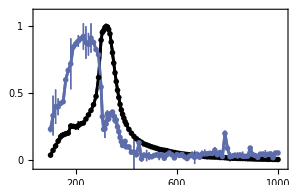
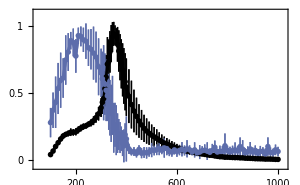
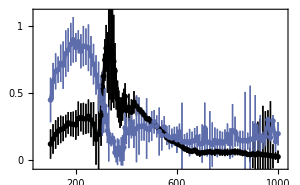
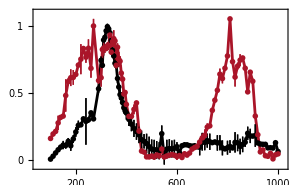
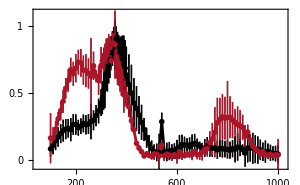
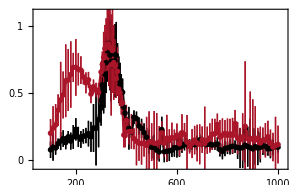
Anopheles |  | 
QUIES | weak SSO | SSO
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{Style[speciesList[[species]],18,Black],SpanFromLeft},Style[#,14,Black]&/@{"QUIES","weak SSO","SSO"},MapThread[
Show[{
ListLinePlot[{envL1TG[[#1]],envN1TG[[#1]]},PlotStyle->{{col1T,AbsoluteThickness[2]},{col1TN,AbsoluteThickness[2]}},opts],
ListLinePlot[{envL1TG[[#1]],envN1TG[[#1]]},PlotStyle->{col1T ,col1TN},PlotMarkers->{fm2["Circle",size,op],fm2["UpTriangle",5]}]}]&,{Range[3]}],
MapThread[
Show[{
ListLinePlot[{envL2TG[[#1]],envN2TG[[#1]]},PlotStyle->{{col2T,AbsoluteThickness[2]},{col2TN,AbsoluteThickness[2]}},opts],
ListPlot[{envL2TG[[#1]],envN2TG[[#1]]},PlotStyle->{col2T,col2TN},PlotMarkers->{fm2["Diamond",size,op2],fm2["DownTriangle",5]}]}]&,{Range[3]}]}]

(*Export[expDir<>"\\sensitivity regions of nerve and flagellum\\"<>"sensitivity region_GROUPED_combined_segment_v.10_NEW DATA_"<>ToString[intensity]<>".svg",%,Background->None]*)
(*Export[expDir<>"\\sensitivity regions of nerve and flagellum\\"<>"sensitivity region_GROUPED_combined_segment_v.10_NEW DATA_"<>ToString[intensity]<>".png",%,ImageResolution->450,Background->None]*)
(*Export[expDir<>"\\sensitivity regions of nerve and flagellum\\"<>speciesList[[species]]<>"_sensitivity region_segment_"<>ToString[intensity]<>".png",%,ImageResolution->450,Background->None]*)
```

```mathematica
quies
wsso
sso
```

{7,9}

{2,6,10,11,17}

{1,3,4,5,8,12,13,14,15,16}

#### Effect to envelope based on stimulus amplitude

```mathematica
Grid[{Style[#,20,Darker@Gray]&/@{"SSO","weak SSO","QUIES"},
Table[
ListLinePlot3D[Table[Insert[int,2]/@avgError[Values[bgRemoval[#,"nerve",int]&/@dat]],{int,1,10}],ImageSize->350,AxesLabel->{"Frequency [Hz]","Stim Intensity [arb]",Rotate["Normalised Nerve response",π/2],Filling->0}],{dat,{sso1T,wsso1T,quies1T}}]}]
```

SSO | weak SSO | QUIES
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Grid[{Style[#,20,Darker@Gray]&/@{"SSO","weak SSO","QUIES"},
Table[
ListLinePlot3D[Table[Insert[int,2]/@avgError[Values[bgRemoval[#,"nerve",int]&/@dat]],{int,1,10}],ImageSize->350,AxesLabel->{"Frequency [Hz]","Stim Intensity [arb]",Rotate["Normalised Nerve response",π/2]}],{dat,{sso2T,wsso2T,quies2T}}]}]
```

SSO | weak SSO | QUIES
-Graphics3D- | -Graphics3D- | -Graphics3D-

#### Effect on envelope based on SSO amplitude

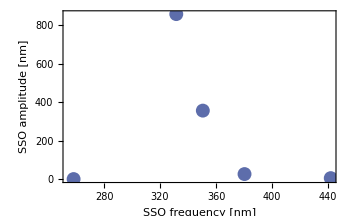

```mathematica
ListPlot[SortBy[MapThread[{StringTake[#1,42;;58]}~Join~(Mean[readMyFile[#][[;;,2]]]&/@{#1,#2})&,{fftfreq,fftamp}],#[[3]]&][[;;,{2,3}]],FrameLabel->{"SSO frequency [nm]","SSO amplitude [nm]"}]
```

```mathematica
joinedData=Join[sso2T,wsso2T,quies2T];
ascendingSSONames=Select[SortBy[MapThread[{StringTake[#1,42;;58]}~Join~(Round@Mean[readMyFile[#][[;;,2]]]&/@{#1,#2})&,{fftfreq,fftamp}],#[[3]]&],Between[#[[2]],{300,400}]&]
ascendingSSOvals=Flatten[Position[Keys[joinedData],#]&/@ascendingSSONames[[;;,1]]];
lgs=MapAt[ToString[#]<>" nm"&,MapAt[ToString[#]<>" Hz"&,SortBy[ascendingSSONames[[Flatten[(Position[ascendingSSONames,#]&/@Keys[joinedData][[ascendingSSOvals]])[[;;,;;,1]]]]],#[[3]]&],{All,2}],{All,3}];
```

{{Mosquito31\set_1\,367,4},{Mosquito28\set_2\,339,5},{Mosquito28\set_1\,381,7},{Mosquito31\set_2\,375,11},{Mosquito30\set_3\,356,30},{Mosquito29\set_1\,371,38},{Mosquito29\set_2\,364,47},{Mosquito30\set_2\,366,54},{Mosquito27\set_3\,384,97},{Mosquito30\set_1\,376,106},{Mosquito27\set_2\,393,124},{Mosquito27\set_1\,392,145},{Mosquito25\set_1\,337,407},{Mosquito25\set_3\,325,606},{Mosquito26\set_2\,333,711},{Mosquito26\set_1\,328,729}}

```mathematica
intensity=5;
ListLinePlot3D[MapThread[Insert[1#1,2]/@#2&,{Range[Length@joinedData[[ascendingSSOvals]]],Values[bgRemoval[#,"nerve",intensity]&/@joinedData[[ascendingSSOvals]]]}],
Filling->Bottom,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Boxed->{Left,Bottom,Back},ImageSize->500,Mesh->All,MeshStyle->{Red, AbsolutePointSize[4]},PlotLegends->Placed[lgs, Right]]
```

-Graphics3D-

### Clustering

I tried all the clustering methods (detailed in OneNote//2-tone//Nerve (stream?) analysis//044_Audibility region based on amplitude).
The best results come from using the “Spectral” clustering method. Mosquito 25 is still classed badly.

```mathematica
test=(Values[wsso1T][[#]]["laser"][[intensity]][[;;,{1,3}]]&/@Range[Length@wsso1T])~Join~(Values[quies1T][[#]]["laser"][[intensity]][[;;,{1,3}]]&/@Range[Length@quies1T])~Join~(Values[sso1T][[#]]["laser"][[intensity]][[;;,{1,3}]]&/@Range[Length@sso1T]);
test2=MapThread[#1->#2&,{test,Join[Keys[wsso1T],Keys[quies1T],Keys[sso1T]]}];
```

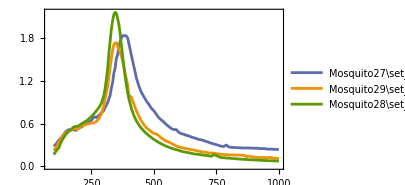
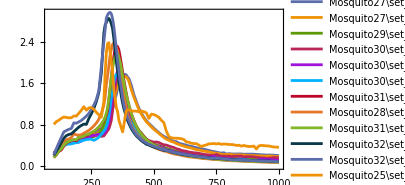
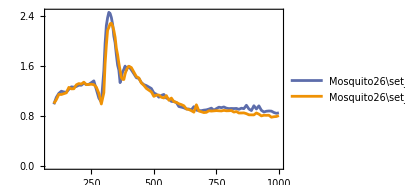

```mathematica
{testOut,testOut2}=FindClusters[#,Method->"Spectral"]&/@{test,test2};
Grid@{{Partition[MapThread[ListLinePlot[#1,PlotLegends->#2,ImageSize->300]&,{testOut,testOut2}],UpTo[2]]}}
```

### PCA

#### PCA on unmodified data

I will apply here my method for PCA.
I need to make sure that all the data I use have the same size everywhere so that I can create a rectangular matrix.
Also, it is important that all rows in place correspond to the same frequencies.

For example, say that I have the following frequencies available for the following mosquitoes:
mosquito 1: {100,110,120,400,1000}
mosquito 2: {100,110,140,500,1000}

These have the same number of points, but i cannot compare the point at 120 Hz of mosquito 1 with the 140 Hz point of mosquito 2. I must make it fair.
Let’s find which are the common frequencies across ALL mosquitoes:

IMPORTANT: The classification of the data was made based on SEGMENT 2. You can easily show that this clustering is highly sensitive to the stimulus amplitude. Although it is true that some animals such as 25, 26, and 27, which are relatively strongly SSOing animals, or at least on the stronger side, are more or less consistently appearing in one corner of the PCA map.

```mathematica
intensity=2;
ch=1; (* whether to look at the laser or nerve data *)
channel={"laser","nerve"};
names=Join[Keys[sso1T],Keys[wsso1T],Keys[quies1T]];
envL=(Values[sso1T][[#]][channel[[ch]]][[intensity]][[;;,{1,3}]]&/@Range[Length@sso1T])~Join~(Values[wsso1T][[#]][channel[[ch]]][[intensity]][[;;,{1,3}]]&/@Range[Length@wsso1T])~Join~(Values[quies1T][[#]][channel[[ch]]][[intensity]][[;;,{1,3}]]&/@Range[Length@quies1T]); (* pool all the envelopes we have *)
allFreqs=Union@@envL[[;;,;;,1]]; (* these are ALL the frequencies that should be present across all animals *)
(*envL//ListPlot*)
```

Unfortunately we have too few points if we want to use the common frequencies. This does not preserve the waveform of the envelopes.
I need to find a better solution.

```mathematica
(*commonFreqs=Intersection@@envL[[;;,;;,1]];
envLclean=Table[Select[dat,MemberQ[commonFreqs,#[[1]]]&],{dat,envL}];
%//ListPlot*)
```

What I can try, is to interpolate the data and use that as my new data.

```mathematica
{min,max}=#[Intersection@@(envL[[;;,;;,1]][[;;,{1,-1}]])ᵀ]&/@{Min, Max} (* find the largest minimum and smallest maximum Frequency that the animals have on record *)
intData=Table[{#,Interpolation[envL[[i]]][#]}&/@Range[min,max,5],{i,Length@envL}];
(*intData//ListPlot*)
zData=Table[(intData[[i,;;,2]]-Mean[intData[[i,;;,2]]])/StandardDeviation[intData[[i,;;,2]]],{i,Length@intData}];
(*zData//ListPlot*)
```

{100,1000}

```mathematica
Mean/@zData
Variance/@zData
```

{-4.9132×10^-16,-1.2973×10^-16,-6.37918×10^-16,-6.50186×10^-16,2.56394×10^-16,2.55167×10^-16,1.13476×10^-15,-1.14089×10^-16,-1.39115×10^-15,3.43494×10^-17,-7.91264×10^-17,9.01673×10^-17,-3.37361×10^-17,-9.13941×10^-17,-9.87546×10^-17,3.98699×10^-17,4.41636×10^-17}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

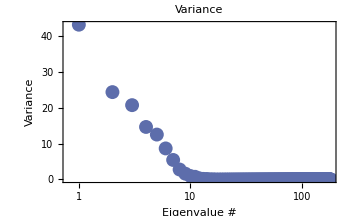
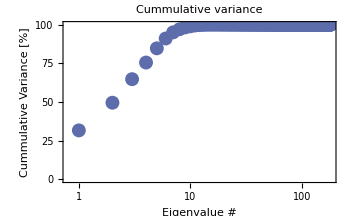

```mathematica
eVals=Eigenvalues[Covariance[zData]];
compMatrix=Eigenvectors[Covariance[zData]]ᵀ; (* the sign of the PComponents is not important*)
scores=Round[zData.compMatrix,0.01];(* calculate PC scores - these are the rotated data*)

varσ=Round[Variance[scores],10^-2];
cumVar=Accumulate[100 Variance[scores]ᵀ/Total[Variance[scores]]]; (* cummulative variance of the eigenvalues *)
(* check that variance is in decreasing order - each corresponds to the eigenvalue of the covariance matrix*)

MapThread[ListPlot[#1,ScalingFunctions->{"Log","Linear"},PlotLabel->#2,FrameLabel->{"Eigenvalue #",#3}]&,{{varσ,cumVar},{"Variance","Cummulative variance"},{"Variance","Cummulative Variance [%]"}}]
```

We can see that ~90% of the variance can be explained by the first two principal components. But let’s use the Kaiser criterion anyway:

```mathematica
method1=Position[cumVar,Select[cumVar,Between[#,{80,100}]&][[1]]][[1,1]] (* the number of principal components to explain 80-100% of the variance *)
method2=Select[varσ,#>=Mean[varσ]&]//Length (* the number of PComponents that meet the Kaiser criterion (larger than the mean of eigenvalues)*)
```

5

10

This is how these eigenvectors look like and perhaps we can make do with just the first two.

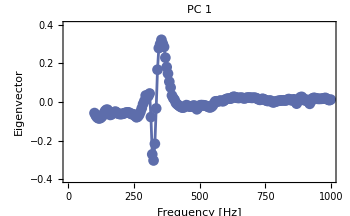
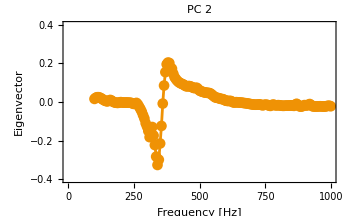
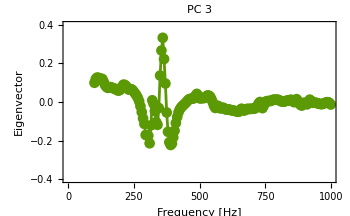
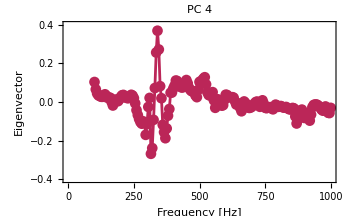
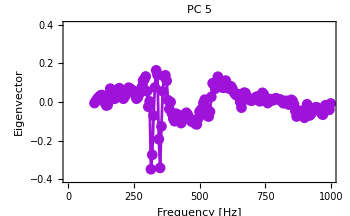
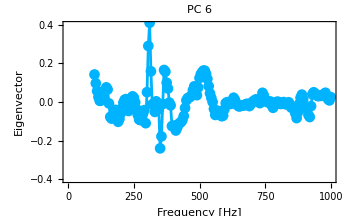

```mathematica
Table[ListLinePlot[{intData[[1,;;,1]],compMatrixᵀ[[i]]}ᵀ,PlotMarkers->Automatic,PlotRange->{-0.4,0.4},PlotStyle->{cols[[i]],AbsolutePointSize[4]},FrameLabel->{"Frequency [Hz]","Eigenvector"},PlotLabel->"PC "<>ToString[i]],{i,6}]
```

```mathematica
compMatrix[[;;,{1,2}]]//Dimensions
```

{181,2}

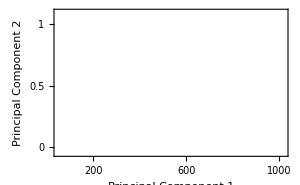
-Graphics-
-Graphics3D-

```mathematica
Grid@{{ListPlot[FindClusters[compMatrix[[;;,{1,2}]],Method->"DBSCAN"],FrameLabel->{"Principal Component 1","Principal Component 2"},Frame->True,opts(*,PlotStyle->({#,AbsolutePointSize[8]}&/@{blue,orange,green})*)]},{
ListPointPlot3D[FindClusters[compMatrix[[;;,{1,2,3}]],Method->"DBSCAN"],AxesLabel->{"PC1","PC2","PC3"},ImageSize->500,PlotRange->Full,AxesStyle->Directive[Black, 16,FontFamily->"Arial",AbsoluteThickness[1.5]]]}}
```

```mathematica
zf=Round[zData.compMatrix,0.01];
pcs=List/@zf[[;;,;;2]];
Manipulate[Show[{ListPlot[pcs,PlotStyle->Directive@{ColorData[97],AbsolutePointSize[10]},FrameLabel->{"Principal Component 1","Principal Component 2"},PlotLabel->"Data in Rotated Frame",PlotLegends->names,Epilog->Inset[names[[i]],Scaled[{0.5,0.5}]],ImageSize->500,PlotRange->Full],
ListPlot[pcs[[i]],PlotStyle->{red,AbsolutePointSize[10]}]}],{i,1,Length@pcs,1},Paneled->False]
```

Part::partd: Part specification names⟦1⟧ is longer than depth of object.

ListPlot::lpn: pcs is not a list of numbers or pairs of numbers.

Part::partd: Part specification pcs⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: pcs⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[pcs,PlotStyle→Directive[{ColorDataFunction[97,Indexed,{«3»},«1»&],AbsolutePointSize[10]}],FrameLabel→{Principal Component 1,Principal Component 2},PlotLabel→Data in Rotated Frame,PlotLegends→names,Epilog→Inset[names⟦1⟧,Scaled[{0.5,0.5}]],ImageSize→500,PlotRange→Full],ListPlot[pcs⟦1⟧,PlotStyle→{color,AbsolutePointSize[10]}]}].

Part::partd: Part specification names⟦1⟧ is longer than depth of object.

ListPlot::lpn: pcs is not a list of numbers or pairs of numbers.

Part::partd: Part specification pcs⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: pcs⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[pcs,PlotStyle→Directive[{ColorDataFunction[97,Indexed,{«3»},«1»&],AbsolutePointSize[10]}],FrameLabel→{Principal Component 1,Principal Component 2},PlotLabel→Data in Rotated Frame,PlotLegends→names,Epilog→Inset[names⟦1⟧,Scaled[{0.5,0.5}]],ImageSize→500,PlotRange→Full],ListPlot[pcs⟦1⟧,PlotStyle→{color,AbsolutePointSize[10]}]}].

Part::partd: Part specification names⟦1⟧ is longer than depth of object.

ListPlot::lpn: pcs is not a list of numbers or pairs of numbers.

Part::partd: Part specification pcs⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: pcs⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[pcs,PlotStyle→Directive[{ColorDataFunction[97,Indexed,{«3»},«1»&],AbsolutePointSize[10]}],FrameLabel→{Principal Component 1,Principal Component 2},PlotLabel→Data in Rotated Frame,PlotLegends→names,Epilog→Inset[names⟦1⟧,Scaled[{0.5,0.5}]],ImageSize→500,PlotRange→Full],ListPlot[pcs⟦1⟧,PlotStyle→{color,AbsolutePointSize[10]}]}].

Part::partd: Part specification names⟦1⟧ is longer than depth of object.

ListPlot::lpn: pcs is not a list of numbers or pairs of numbers.

Part::partd: Part specification pcs⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: pcs⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[pcs,PlotStyle→Directive[{ColorDataFunction[97,Indexed,{«3»},«1»&],AbsolutePointSize[10]}],FrameLabel→{Principal Component 1,Principal Component 2},PlotLabel→Data in Rotated Frame,PlotLegends→names,Epilog→Inset[names⟦1⟧,Scaled[{0.5,0.5}]],ImageSize→500,PlotRange→Full],ListPlot[pcs⟦1⟧,PlotStyle→{color,AbsolutePointSize[10]}]}].

Part::partd: Part specification names⟦1⟧ is longer than depth of object.

ListPlot::lpn: pcs is not a list of numbers or pairs of numbers.

Part::partd: Part specification pcs⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: pcs⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[pcs,PlotStyle→Directive[{ColorDataFunction[97,Indexed,{«3»},«1»&],AbsolutePointSize[10]}],FrameLabel→{Principal Component 1,Principal Component 2},PlotLabel→Data in Rotated Frame,PlotLegends→names,Epilog→Inset[names⟦1⟧,Scaled[{0.5,0.5}]],ImageSize→500,PlotRange→Full],ListPlot[pcs⟦1⟧,PlotStyle→{color,AbsolutePointSize[10]}]}].

Part::partd: Part specification names⟦1⟧ is longer than depth of object.

ListPlot::lpn: pcs is not a list of numbers or pairs of numbers.

Part::partd: Part specification pcs⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: pcs⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[pcs,PlotStyle→Directive[{ColorDataFunction[97,Indexed,{«3»},«1»&],AbsolutePointSize[10]}],FrameLabel→{Principal Component 1,Principal Component 2},PlotLabel→Data in Rotated Frame,PlotLegends→names,Epilog→Inset[names⟦1⟧,Scaled[{0.5,0.5}]],ImageSize→500,PlotRange→Full],ListPlot[pcs⟦1⟧,PlotStyle→{color,AbsolutePointSize[10]}]}].

Part::partd: Part specification names⟦1⟧ is longer than depth of object.

ListPlot::lpn: pcs is not a list of numbers or pairs of numbers.

Part::partd: Part specification pcs⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: pcs⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[pcs,PlotStyle→Directive[{ColorDataFunction[97,Indexed,{«3»},«1»&],AbsolutePointSize[10]}],FrameLabel→{Principal Component 1,Principal Component 2},PlotLabel→Data in Rotated Frame,PlotLegends→names,Epilog→Inset[names⟦1⟧,Scaled[{0.5,0.5}]],ImageSize→500,PlotRange→Full],ListPlot[pcs⟦1⟧,PlotStyle→{color,AbsolutePointSize[10]}]}].

```mathematica
quies
```

{1,3,4,5}

```mathematica
pcs3D=zf[[;;,;;3]];
{mthd,distFunc}={"DBSCAN",ChebyshevDistance};
pcs3Dnames=FindClusters[Normal[AssociationThread[zf[[;;,;;3]],StringReplace[names,"Mosquito"->"Mos "]]],Method->mthd];
pcsLgnd=Column[#,Frame->True]&/@Sort/@pcs3Dnames;
ListPointPlot3D[FindClusters[pcs3D,Method->mthd],PlotStyle->Directive@{ColorData[97],AbsolutePointSize[10]},AxesLabel->{"Principal Component 1","Principal Component 2",Rotate["Principal Component 3",π/2]},PlotLabel->"Data in Rotated Frame",ImageSize->500,Filling->Bottom,FillingStyle->{Opacity[0.8]},PlotTheme->"Web",PlotLegends->pcsLgnd]
```

-Graphics3D-

```mathematica
quies
wsso
sso
```

{7,9}

{2,6,10,11,17}

{1,3,4,5,8,12,13,14,15,16}

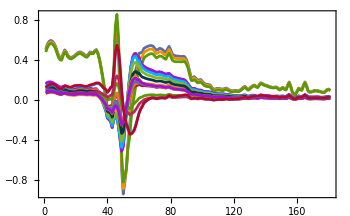

```mathematica
zfilt=zf;
zfilt[[;;,3;;]]=0;
zFilt=zfilt.Inverse[compMatrix];
ListLinePlot[zFilt]
```

#### PCA on baseline-subtracted data

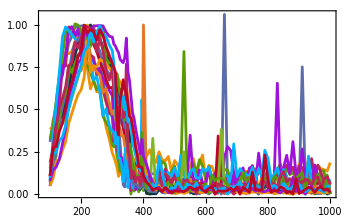
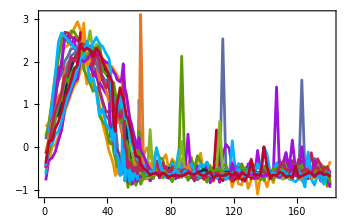

```mathematica
intensity=2;
ch=2;
channel={"laser","nerve"};
names=Join[Keys[sso1T],Keys[wsso1T],Keys[quies1T]];
envL=Flatten[Values/@MapThread[bgRemoval[#,channel[[ch]],2]&/@#1&,{{sso1T,wsso1T,quies1T}}],1]; (* pool all the envelopes we have *)
allFreqs=Union@@envL[[;;,;;,1]]; (* these are ALL the frequencies that should be present across all animals *)
{min,max}=#[Intersection@@(envL[[;;,;;,1]][[;;,{1,-1}]])ᵀ]&/@{Min, Max} ;(* find the largest minimum and smallest maximum Frequency that the animals have on record *)
intData=Table[{#,Interpolation[envL[[i]],InterpolationOrder->1][#]}&/@Range[min,max,5],{i,Length@envL}];


(* either use this line to keep it as is *)
(*zData=intData[[;;,;;,2]];*) 
zData=Table[(intData[[i,;;,2]]-Mean[intData[[i,;;,2]]])/StandardDeviation[intData[[i,;;,2]]],{i,Length@intData}];(* or use this line to standardise the data -Marcos asked that we do not standardise *)
ListLinePlot/@{envL,zData}
```

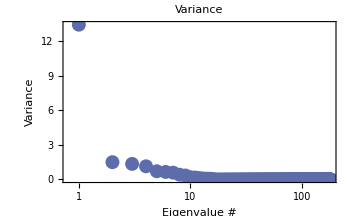
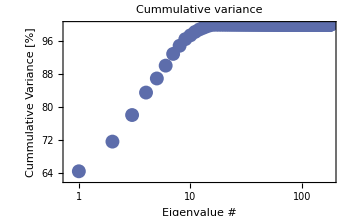

```mathematica
eVals=Eigenvalues[Covariance[zData]];
compMatrix=Eigenvectors[Covariance[zData]]ᵀ; (* the sign of the PComponents is not important*)
scores=Round[zData.compMatrix,0.01];(* calculate PC scores - these are the rotated data*)

varσ=Round[Variance[scores],10^-2];
cumVar=Accumulate[100 Variance[scores]ᵀ/Total[Variance[scores]]]; (* cummulative variance of the eigenvalues *)
(* check that variance is in decreasing order - each corresponds to the eigenvalue of the covariance matrix*)

zf=Round[zData.compMatrix,0.01];

MapThread[ListPlot[#1,ScalingFunctions->{"Log","Linear"},PlotLabel->#2,FrameLabel->{"Eigenvalue #",#3}]&,{{varσ,cumVar},{"Variance","Cummulative variance"},{"Variance","Cummulative Variance [%]"}}]
```

```mathematica
method1=Position[cumVar,Select[cumVar,Between[#,{80,100}]&][[1]]][[1,1]] (* the number of principal components to explain 80-100% of the variance *)
method2=Select[varσ,#>=Mean[varσ]&]//Length (* the number of PComponents that meet the Kaiser criterion (larger than the mean of eigenvalues)*)
```

4

12

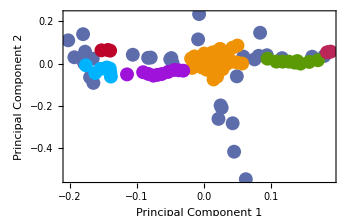
-Graphics- | -Graphics3D-

```mathematica
Grid@{{ListPlot[FindClusters[compMatrix[[;;,{1,2}]],Method->"DBSCAN"],FrameLabel->{"Principal Component 1","Principal Component 2"}],
ListPointPlot3D[FindClusters[compMatrix[[;;,{1,2,3}]],Method->"DBSCAN"],AxesLabel->{"Principal Component 1","Principal Component 2","PC3"},ImageSize->500]}}
```

```mathematica
pcs3D=zf[[;;,;;3]];
{mthd,distFunc}={"DBSCAN",ChebyshevDistance};
pcs3Dnames=FindClusters[Normal[AssociationThread[zf[[;;,;;3]],StringReplace[names,"Mosquito"->"Mos "]]],Method->mthd];
pcsLgnd=Column[#,Frame->True]&/@Sort/@pcs3Dnames;
ListPointPlot3D[FindClusters[pcs3D,Method->mthd],PlotStyle->Directive@{ColorData[97],AbsolutePointSize[10]},AxesLabel->{"Principal Component 1","Principal Component 2",Rotate["Principal Component 3",π/2]},PlotLabel->"Data in Rotated Frame",ImageSize->500,Filling->Bottom,FillingStyle->{Opacity[0.8]},PlotTheme->"Web",PlotLegends->pcsLgnd]
```

-Graphics3D-

## Identifying DPs in ROI

### Overall contribution

```mathematica
Flatten[ssoDist1T][[1]]
ToExpression@StringCases[StringSplit[%,"_"][[-2]],DigitCharacter..]=={100,1000}
```

M:\Documents\Alex\UCL_data\2022 - 2 tone\Mosquito25\set_1\Nerve\M_AGA_Kisumu_ZT11_2023-02-14_No 001_1TN_dictContribution_Stim [100-1000]_Resp [0-1200].txt

True

```mathematica
Clear[segFinder]
segFinder[string_,range_]:=Select[Flatten[string],ToExpression@StringCases[StringSplit[#,"_"][[-2]],DigitCharacter..]==range&]
```

```mathematica
ssoDist1T=FileNames["*"<>"1TN_dictContribution_Stim"<>"*"<>".txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\"<>#,4]&/@Keys[sso1T];
ssoDist2T=FileNames["*"<>"2TN_dictContribution_Stim"<>"*"<>".txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\"<>#,4]&/@Keys[sso1T];

mosNames=StringReplace[StringTake[ssoDist1T[[#,1]],{42,57}],"Mosquito"->"mos_"]&/@Range[Length@ssoDist1T];
ssoPart1of31T=Import[#,"JSON"]&/@segFinder[ssoDist1T,{100,300}]; (* this corresponds to the 100-400 Hz regime *)
ssoPart2of31T=Import[#,"JSON"]&/@segFinder[ssoDist1T,{400,600}]; (* this corresponds to the 400-600 Hz regime *)
ssoPart3of31T=Import[#,"JSON"]&/@segFinder[ssoDist1T,{600,1000}]; (* this corresponds to the 600-1000 Hz regime *)
ssoPartTotal1T=Import[#,"JSON"]&/@segFinder[ssoDist1T,{100,1000}]; (* this corresponds to the 100-1000 Hz regime *)
ssoPartEntrainment1T=Import[#,"JSON"]&/@segFinder[ssoDist1T,{300,400}]; (* this corresponds to the 300-400 Hz regime *)

ssoPart1of32T=Import[#,"JSON"]&/@segFinder[ssoDist2T,{100,300}]; (* this corresponds to the 100-400 Hz regime *)
ssoPart2of32T=Import[#,"JSON"]&/@segFinder[ssoDist2T,{400,600}]; (* this corresponds to the 400-600 Hz regime *)
ssoPart3of32T=Import[#,"JSON"]&/@segFinder[ssoDist2T,{600,1000}]; (* this corresponds to the 600-1000 Hz regime *)
ssoPartTotal2T=Import[#,"JSON"]&/@segFinder[ssoDist2T,{100,1000}]; (* this corresponds to the 100-1000 Hz regime *)
ssoPartEntrainment2T=Import[#,"JSON"]&/@segFinder[ssoDist2T,{300,400}]; (* this corresponds to the 300-400 Hz regime *)
```

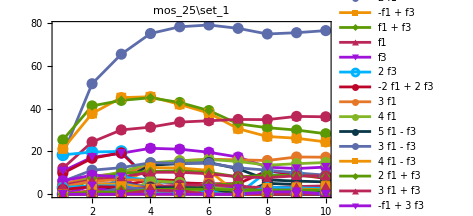
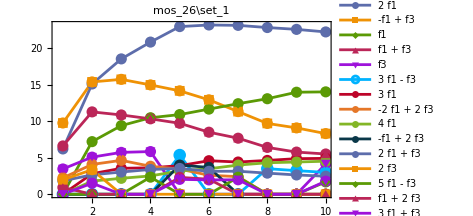
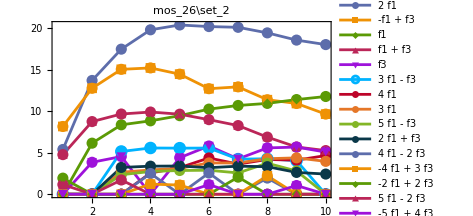
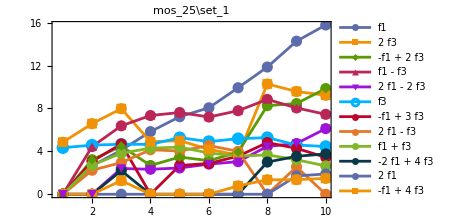
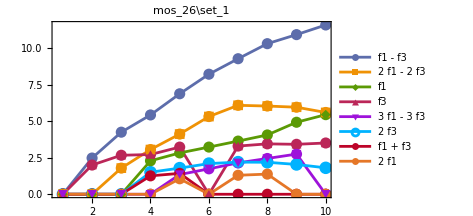
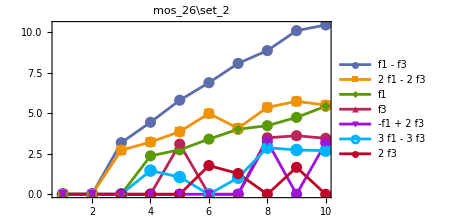
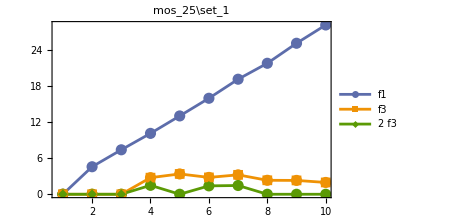
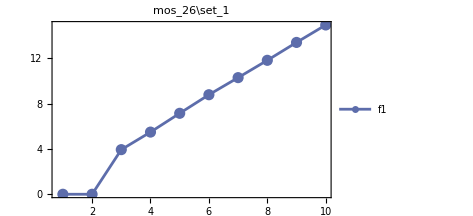

```mathematica
Table[MapThread[ListLinePlot[Values/@Values[#1]/.""->0,Mesh->All,MeshStyle->AbsolutePointSize[8],PlotLegends->Placed[Keys[#],Bottom],PlotMarkers->{Automatic, 10},PlotLabel->#2]&,{dat,mosNames,{"[100-400] Hz","[400-600] Hz","[600,1000] Hz"}}],{dat,{ssoPart1of31T,ssoPart2of31T,ssoPart3of31T}}]
```

```mathematica
Clear[DPfraction]
DPfraction[data_,percentage_:80]:=Block[{DPval,perc80},
(* this code assumes that the data you feed it contains information of the integrated data of a DPTrace over a specific span (i.e. 100-400 Hz).
It will find the percentile contribution of that DP within that frequency range *)
DPval={Keys[data],Round[(Total/@Values[Values[data]]/.""->0)/Total[Total/@Values[Values[data]]/.""->0]100,0.1]}ᵀ(* percentile contribution of a DP within its own group *);
perc80=Position[Accumulate[DPval[[;;,2]]],Select[Accumulate[DPval[[;;,2]]],#>=percentage&][[1]]][[1,1]] (* finds at which point >=80% of the contribution is accounted for*);
DPval[[;;perc80]]~Join~{{"Other",Total[DPval[[perc80+1;;,2]]]}}
](* end of block*)
DPfraction[ssoPart1of31T[[1]]]
```

Part::partd: Part specification ssoPart1of31T⟦1⟧ is longer than depth of object.

Keys::invrl: The argument ssoPart1of31T⟦1⟧ is not a valid Association or a list of rules.

Values::invrl: The argument ssoPart1of31T⟦1⟧ is not a valid Association or a list of rules.

Values::invrl: The argument Values[ssoPart1of31T⟦1⟧] is not a valid Association or a list of rules.

Values::invrl: The argument Total[Values[ssoPart1of31T⟦1⟧]] is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Part::partw: Part 2 of Keys[ssoPart1of31T⟦1⟧] does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 1 of Part[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+{}⟦1,1⟧;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Join[{Keys[ssoPart1of31T⟦1⟧],Round[(100 Values[Total[Values[ssoPart1of31T⟦1⟧]]])/Total[Values[Total[Values[ssoPart1of31T⟦1⟧]]]],0.1]}⟦1;;{}⟦1,1⟧⟧,{{Other,Total[{Keys[ssoPart1of31T⟦1⟧],Round[(100 Values[Total[Values[ssoPart1of31T⟦1⟧]]])/Total[Values[Total[Values[ssoPart1of31T⟦1⟧]]]],0.1]}⟦1+{}⟦1,1⟧;;All,2⟧]}}]

```mathematica
Clear[DPfractionAVG]
DPfractionAVG[data_,percentage_:80]:=Block[{DPval,gathData,perc80},
DPval=Flatten[MapThread[{#1,#2}ᵀ&,{
Keys/@data,(* find all the keys for each mosquito *)
Table[Round[(Total/@Values[Values[mosquito]]/.""->0)/Total[Total/@Values[Values[mosquito]]/.""->0]100,0.1],{mosquito,data}]}](* total each DP and create a percentage of all of them *)
,1](* flatten all mosquitoes *);
gathData=(GatherBy[DPval,#[[1]]&]);
DPval=ReverseSortBy[{gathData[[;;,1,1]],Round[Total[#[[;;,2]]]/Length[data]&/@gathData,0.1]}ᵀ,#[[2]]&];
perc80=Position[Accumulate[DPval[[;;,2]]],Select[Accumulate[DPval[[;;,2]]],#>=percentage&][[1]]][[1,1]] (* finds at which point >=80% of the contribution is accounted for*);
DPval[[;;perc80]]~Join~{{"Other",Total[DPval[[perc80+1;;,2]]]}}
](*end of block*)
DPfractionAVG[ssoPart1of31T]
```

Table::iterb: Iterator {mosquito,ssoPart1of31T} does not have appropriate bounds.

MapThread::mptd: Object ssoPart1of31T at position {2, 1} in MapThread[{&,{ssoPart1of31T,Table[Round[((Map[«2»]/.Rule[«2»]) 100)/Total[«1»],0.1],{mosquito,ssoPart1of31T}]}] has only 0 of required 1 dimensions.

GatherBy::list: List expected at position 1 in GatherBy[MapThread[{&,{ssoPart1of31T,Table[Round[(ReplaceAll[«2»] Power[«2»]) 100,0.1],{mosquito,ssoPart1of31T}]}],#1⟦1⟧&].

Part::partw: Part 2 of {& does not exist.

Power::infy: Infinite expression 1/0 encountered.

GatherBy::list: List expected at position 1 in GatherBy[ComplexInfinity,ComplexInfinity].

Transpose::nmtx: The first two levels of {{{#1},{#2}},Round[GatherBy[ComplexInfinity,ComplexInfinity],0.1]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+{}⟦1,1⟧;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Join[Transpose[{{{#1},{#2}},Round[GatherBy[ComplexInfinity,ComplexInfinity],0.1]}]⟦1;;{}⟦1,1⟧⟧,{{Other,Total[Transpose[{{{#1},{#2}},Round[GatherBy[ComplexInfinity,ComplexInfinity],0.1]}]⟦1+{}⟦1,1⟧;;All,2⟧]}}]

```mathematica
BarChart[Reverse[Callout[#[[2]],#[[1]]]&/@DPfraction[ssoPart1of31T[[1]]]],ChartLayout->"Stacked",ChartLabels->{{"[100-400]","[400-600]","[600-1000]"},None},BarSpacing->2]
```

-Graphics-

```mathematica
Grid[{{BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@DPfractionAVG[dat]],{dat,{ssoPart1of31T,ssoPart2of31T,ssoPart3of31T}}],ChartLayout->"Stacked",ChartLabels->{Style[#,10,Black]&/@{"[100-400]","[400-600]","[600-1000]"},None},BarSpacing->1.5,ImageSize->500],
BarChart[{Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")",Above]&/@DPfractionAVG[ssoPart1of31T]]},ChartLayout->"Stepped",ChartLabels->{Style[#,10,Black]&/@{"[100-400]","[400-600]","[600-1000]"},None},BarSpacing->0.1,ImageSize->500]}}]
```

-Graphics-

```mathematica
(* SSO animals*)
datSSO={{ssoPart1of31T,ssoPartEntrainment1T,ssoPart2of31T,ssoPart3of31T},{ssoPart1of32T,ssoPartEntrainment2T,ssoPart2of32T,ssoPart3of32T}};
labelSSO={"[100-300]","[300-400]","[400-600]","[600-1000]"};
Grid[{{BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@DPfractionAVG[dat]],{dat,datSSO[[1]]}],ChartLayout->"Stacked",ChartLabels->{labelSSO,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["one-tone",18,Black]],BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@DPfractionAVG[dat,80]],{dat,datSSO[[2]]}],ChartLayout->"Stacked",ChartLabels->{labelSSO,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["two-tone",18,Black]]}}]
```

-Graphics-

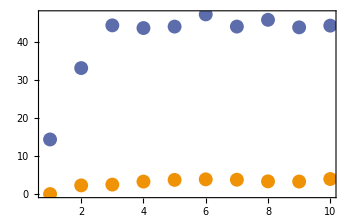

```mathematica
ListPlot[Table[Mean[Values[<|#|>[dp]/.""->0&/@ssoPart1of32T]],{dp,{"-f1 + f2","2 f1 - f2"}}]]
```

```mathematica
(* wSSO animals*)
wssoDist1T=FileNames["*"<>"1TN_dictContribution_Stim"<>"*"<>".txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\"<>#,4]&/@Keys[wsso1T];
wssoDist2T=FileNames["*"<>"2TN_dictContribution_Stim"<>"*"<>".txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\"<>#,4]&/@Keys[wsso1T];

wssoPart1of31T=Import[#,"JSON"]&/@segFinder[wssoDist1T,{100,300}]; (* this corresponds to the 100-400 Hz regime *)
wssoPart2of31T=Import[#,"JSON"]&/@segFinder[wssoDist1T,{400,600}]; (* this corresponds to the 400-600 Hz regime *)
wssoPart3of31T=Import[#,"JSON"]&/@segFinder[wssoDist1T,{600,1000}]; (* this corresponds to the 600-1000 Hz regime *)
wssoPartTotal1T=Import[#,"JSON"]&/@segFinder[wssoDist1T,{100,1000}]; (* this corresponds to the 100-1000 Hz regime *)
wssoPartEntrainment1T=Import[#,"JSON"]&/@segFinder[wssoDist1T,{300,400}]; (* this corresponds to the 300-400 Hz regime *)

wssoPart1of32T=Import[#,"JSON"]&/@segFinder[wssoDist2T,{100,300}]; (* this corresponds to the 100-400 Hz regime *)
wssoPart2of32T=Import[#,"JSON"]&/@segFinder[wssoDist2T,{400,600}]; (* this corresponds to the 400-600 Hz regime *)
wssoPart3of32T=Import[#,"JSON"]&/@segFinder[wssoDist2T,{600,1000}]; (* this corresponds to the 600-1000 Hz regime *)
wssoPartTotal2T=Import[#,"JSON"]&/@segFinder[wssoDist2T,{100,1000}]; (* this corresponds to the 100-1000 Hz regime *)
wssoPartEntrainment2T=Import[#,"JSON"]&/@segFinder[wssoDist2T,{300,400}]; (* this corresponds to the 300-400 Hz regime *)
```

```mathematica
datwSSO={{wssoPart1of31T,wssoPartEntrainment1T,wssoPart2of31T,wssoPart3of31T},{wssoPart1of32T,wssoPartEntrainment2T,wssoPart2of32T,wssoPart3of32T}};
labelwSSO={"[100-300]","[300-400]","[400-600]","[600-1000]"};
Grid[{{BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@DPfractionAVG[dat]],{dat,datwSSO[[1]]}],ChartLayout->"Stacked",ChartLabels->{labelwSSO,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["one-tone",18,Black]],BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@DPfractionAVG[dat,80]],{dat,datwSSO[[2]]}],ChartLayout->"Stacked",ChartLabels->{labelwSSO,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["two-tone",18,Black]]}}]
```

-Graphics-

```mathematica
(* QUIES animals*)
qDist1T=FileNames["*"<>"1TN_dictContribution_Stim"<>"*"<>".txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\"<>#,4]&/@Keys[quies1T];
qDist2T=FileNames["*"<>"2TN_dictContribution_Stim"<>"*"<>".txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\"<>#,4]&/@Keys[quies2T];

qPart1of31T=Import[#,"JSON"]&/@segFinder[qDist1T,{100,300}]; (* this corresponds to the 100-400 Hz regime *)
qPart2of31T=Import[#,"JSON"]&/@segFinder[qDist1T,{400,600}]; (* this corresponds to the 400-600 Hz regime *)
qPart3of31T=Import[#,"JSON"]&/@segFinder[qDist1T,{600,1000}]; (* this corresponds to the 600-1000 Hz regime *)
qPartTotal1T=Import[#,"JSON"]&/@segFinder[qDist1T,{100,1000}]; (* this corresponds to the 100-1000 Hz regime *)
qPartEntrainment1T=Import[#,"JSON"]&/@segFinder[qDist1T,{300,400}]; (* this corresponds to the 300-400 Hz regime *)

qPart1of32T=Import[#,"JSON"]&/@segFinder[qDist2T,{100,300}]; (* this corresponds to the 100-400 Hz regime *)
qPart2of32T=Import[#,"JSON"]&/@segFinder[qDist2T,{400,600}]; (* this corresponds to the 400-600 Hz regime *)
qPart3of32T=Import[#,"JSON"]&/@segFinder[qDist2T,{600,1000}]; (* this corresponds to the 600-1000 Hz regime *)
qPartTotal2T=Import[#,"JSON"]&/@segFinder[qDist2T,{100,1000}]; (* this corresponds to the 100-1000 Hz regime *)
qPartEntrainment2T=Import[#,"JSON"]&/@segFinder[qDist2T,{300,400}]; (* this corresponds to the 300-400 Hz regime *)
```

```mathematica
datQ={{qPart1of31T,qPartEntrainment1T,qPart2of31T,qPart3of31T},{qPart1of32T,qPartEntrainment2T,qPart2of32T,qPart3of32T}};
labelQ={"[100-300]","[300-400]","[400-600]","[600-1000]"};
Grid[{{BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@DPfractionAVG[dat]],{dat,datQ[[1]]}],ChartLayout->"Stacked",ChartLabels->{labelQ,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["one-tone",18,Black]],BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@DPfractionAVG[dat,80]],{dat,datQ[[2]]}],ChartLayout->"Stacked",ChartLabels->{labelQ,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["two-tone",18,Black](*,Background->hexToRGB["#404040"],AxesStyle->Directive[White,16,AbsoluteThickness[1.5]]*)]}}]
```

-Graphics-

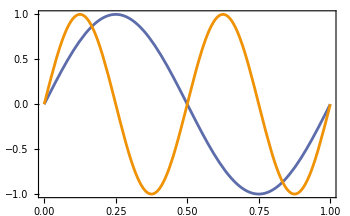

```mathematica
Plot[{1(Sin[2π 1x]+Sin[2π 1 +π/2])-1,Sin[2π 2x]},{x,0,1}]
```

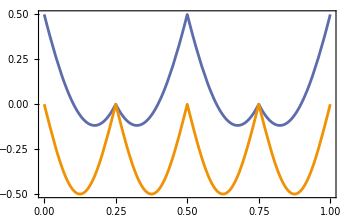

```mathematica
Plot[{(-Abs@Sin[2π 1x]-0.5Abs@Sin[2π 1x+π/2])+1, -0.5Abs@Sin[2π 2x]},{x,0,1}]
```

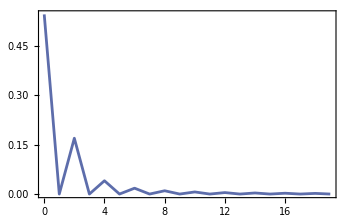

```mathematica
fourier[Table[(-Abs@Sin[2π 0.5x]+-Abs@Sin[2π 0.5x+π/2])+1,{x,0,1-1/1000,1/1000}],1000,20]//ListLinePlot
```

### Grouped harmonics

This section will try to explore how these bar charts will look like if we were to count the combined contribution of a DP as well as its harmonics. 
For example the f2-f1 DP will incorporate the 2(f2-f1), 3(f2-f1),.... etc.
I am not certain whether this is a wise thing to do as some contributions are more powerful in the 2nd harmonic.
But the sheer number of distortions in the 2T case is staggering.

```mathematica
Clear[groupedDP]
groupedDP[data_]:=Block[{t,t2,t3,t4},
(* I want create a function that creates a collective contribution from a family of DPs.
This function needs to be able to algebraically identify DPs and group them together.
Numerical approaches should not be used as there are many DPs which form numerical identity.
 *)
(* Step1: perform the standard DPfractionAVG analysis and convert DP to expression*)
t=ToExpression[DPfractionAVG[data,80]] ;
(* Step 2: Group the DPs based on which variables are in play. For example, f2-f1 and 2f1+3f2 will be in the same group. This avoids issues with grouping f1-f3 and f1-f2 *)
t2=GatherBy[t,Variables[#[[1]]]&];
(* Step 3: For every grouping do the following:
a. Calculate the CoefficientList, which should give a unique list of coefficients for each DP within that group.
b. Group the DPs into families based on the coefficient list. Each DP family must have a common GCD. Idea inspired from here:
https://mathematica.stackexchange.com/questions/157783/test-if-a-list-is-a-constant-integer-multiple-of-another-list.
c. Drop the coefficient list, keeping only the DP name and contribution.
NOTE: You may choose to not sort each family by lowest order (default). This means that the family name is given by the strongest family member.*)
t3=Table[(*Sort[#]*)#[[;;,{2,3}]]&/@GatherBy[({Flatten[CoefficientList[#,{f1,f2,f3}]]&/@group[[;;,1]],group[[;;,1]],group[[;;,2]]}ᵀ),#[[1]]/Max[1,GCD@@#[[1]]]&],{group,t2}];
(* Step 4: For each family extract the base DP name and sum the contributions from all family members. Do this for all DP groups and families. *)
t4=Flatten[Table[{ToString[t3[[group,family,1,1]]],Total[t3[[group,family]][[;;,2]]]},{group,Length@t3},{family,Length@t3[[group]]}],1];
ReverseSortBy[t4[[;;-2]],#[[2]]&]~Join~{t4[[-1]]}
]
groupedDP[ssoPart1of32T]
```

Table::iterb: Iterator {mosquito,ssoPart1of32T} does not have appropriate bounds.

MapThread::mptd: Object ssoPart1of32T at position {2, 1} in MapThread[{&,{ssoPart1of32T,Table[Round[((Map[«2»]/.Rule[«2»]) 100)/Total[«1»],0.1],{mosquito,ssoPart1of32T}]}] has only 0 of required 1 dimensions.

GatherBy::list: List expected at position 1 in GatherBy[MapThread[{&,{ssoPart1of32T,Table[Round[(ReplaceAll[«2»] Power[«2»]) 100,0.1],{mosquito,ssoPart1of32T}]}],#1⟦1⟧&].

Part::partw: Part 2 of {& does not exist.

Power::infy: Infinite expression 1/0 encountered.

GatherBy::list: List expected at position 1 in GatherBy[ComplexInfinity,ComplexInfinity].

Transpose::nmtx: The first two levels of {{{#1},{#2}},Round[GatherBy[ComplexInfinity,ComplexInfinity],0.1]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+{}⟦1,1⟧;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

ToExpression::notstrbox: Join[{⟦1;;{}⟦1,1⟧⟧,{{Other,Total[{⟦1+Part[«3»];;All,2⟧]}}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

GatherBy::list: List expected at position 1 in GatherBy[$Failed,Variables[#1⟦1⟧]&].

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

Table::iterb: Iterator {group,GatherBy[$Failed,Variables[#1⟦1⟧]&]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partd: Part specification Table[(#1⟦1;;All,{2,3}⟧&)/@GatherBy[{,(Slot[«1»]⟦1⟧)/Max[«2»]&],{group,GatherBy[$Failed,Variables[Slot[«1»]⟦1⟧]&]}]⟦2,1,1,1⟧ is longer than depth of object.

Part::partd: Part specification Table[(#1⟦1;;All,{2,3}⟧&)/@GatherBy[{,(Slot[«1»]⟦1⟧)/Max[«2»]&],{group,GatherBy[$Failed,Variables[Slot[«1»]⟦1⟧]&]}]⟦2,2,1,1⟧ is longer than depth of object.

Part::partd: Part specification GatherBy[$Failed,Variables[#1⟦1⟧]&]⟦1;;All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{                                                                                                                                                                                   #1[[1]]
Table[(#1[[1 ;; All,{2, 3}]] & ) /@ GatherBy[Transpose[{(Flatten[CoefficientList[#1, {f1, f2, f3}]] & ) /@ group[[1 ;; All,1]], group[[1 ;; All,1]], group[[1 ;; All,2]]}], ---------------------- & ], {group, GatherBy[$Failed, Variables[#1[[1]]] & ]}][[2,1,1,1]]
                                                                                                                                                                            Max[1, GCD @@ #1[[1]]],Total[Integer[]]},{#1,Total[1;;All&]},{                                                                                                                                                                                   #1[[1]]
Table[(#1[[1 ;; All,{2, 3}]] & ) /@ GatherBy[Transpose[{(Flatten[CoefficientList[#1, {f1, f2, f3}]] & ) /@ group[[1 ;; All,1]], group[[1 ;; All,1]], group[[1 ;; All,2]]}], ---------------------- & ], {group, GatherBy[$Failed, Variables[#1[[1]]] & ]}][[2,2,1,1]]
                                                                                                                                                                            Max[1, GCD @@ #1[[1]]],Total[GatherBy[$Failed,Variables[#1⟦1⟧]&]⟦1;;All,2⟧]}}

```mathematica
Length/@{DPfractionAVG[ssoPart1of32T,80],groupedDP[ssoPart1of32T]}
Length/@{DPfractionAVG[wssoPart1of32T,80],groupedDP[wssoPart1of32T]}
Length/@{DPfractionAVG[qPart1of32T,80],groupedDP[qPart1of32T]}
```

{35,28}

{24,18}

{20,14}

```mathematica
Grid[{{BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@groupedDP[dat]],{dat,datSSO[[1]]}],ChartLayout->"Stacked",ChartLabels->{labelSSO,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["one-tone",18,Black]],BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@groupedDP[dat]],{dat,datSSO[[2]]}],ChartLayout->"Stacked",ChartLabels->{labelSSO,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["two-tone",18,Black]]}}]
```

-Graphics-

```mathematica
Grid[{{BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@groupedDP[dat]],{dat,datwSSO[[1]]}],ChartLayout->"Stacked",ChartLabels->{labelwSSO,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["one-tone",18,Black]],BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@groupedDP[dat]],{dat,datwSSO[[2]]}],ChartLayout->"Stacked",ChartLabels->{labelwSSO,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["two-tone",18,Black]]}}]
```

-Graphics-

```mathematica
Grid[{{BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@groupedDP[dat]],{dat,datQ[[1]]}],ChartLayout->"Stacked",ChartLabels->{labelQ,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["one-tone",18,Black]],BarChart[Table[Reverse[Callout[#[[2]],ToString[Round[#[[2]]]]<> "% ("<>#[[1]]<>")"]&/@groupedDP[dat]],{dat,datQ[[2]]}],ChartLayout->"Stacked",ChartLabels->{labelQ,None},BarSpacing->1.5,ImageSize->600,PlotLabel->Style["two-tone",18,Black]]}}]
```

-Graphics-

```mathematica
540/200.
```

2.7

```mathematica
540/1.666
```

324.13

### Segmented contribution

#### Individual animals

```mathematica
Clear[DPfractionSeg]
DPfractionSeg[data_,seg_:1,perc_:80]:=Block[{vals,total,percCutOff},
(* this breaks down the DP contribution for ONE mosquito on a segment by segment basis *)
vals=Values[Values[data/.""->0][[;;,seg]]];
vals=Round[vals/Total[vals]100,0.1];
percCutOff=Position[Accumulate[vals],Select[Accumulate[vals],#>=perc&][[1]]][[1,1]] (* finds at which point >=80% of the contribution is accounted for*);
ReverseSortBy[{Keys[data][[;;percCutOff]],vals[[;;percCutOff]]}ᵀ,#[[2]]&]~Join~{{"Other",Total@vals[[percCutOff+1;;]]}}

](* end of block*)
(*DPfractionSeg[ssoPart1of3[[1]],1]*)
```

```mathematica
BarChart[Table[Reverse[Callout[#[[2]],#[[1]]<> " ("<>ToString[Round[#[[2]]]]<>"%)"]&/@DPfractionSeg[ssoPart1of31T[[1]],i]],{i,10}],ChartLayout->"Stacked",BarSpacing->1]
```

-Graphics-

```mathematica
t=GatherBy[Flatten[Table[Insert[#,i,1]&/@DPfractionSeg[ssoPart1of3[[1]],i],{i,10}],1],#[[2]]&];
t2=Table[If[Length[t[[j]]]==10,Sort[t[[j]],#[[1]]&],SortBy[Table[{i,t[[j,1,2]],0},{i,Complement[Range[10],t[[j,;;,1]]]}]~Join~t[[j]],#[[1]]&]],{j,10}][[;;,;;,{2,3}]];
```

```mathematica
ParallelAxisPlot[List/@t2[[;;,;;,2]],PlotRange->{0,30},LabelingFunction->(Callout[Part[List/@t2[[;;,1,1]],Sequence@@#2]]&),PlotMarkers->Automatic,PlotLegends->t2[[;;,1,1]],ImageSize->600]
```

-Graphics-

#### Averaged animals

```mathematica
Clear[DPfractionSegAVG]
DPfractionSegAVG[data_,seg_:1,percentage_:80]:=Block[{vals,percCutOff,gathData,DPval},
(* this breaks down the DP contribution for ONE mosquito on a segment by segment basis *)
vals=Values[Values[data/.""->0][[;;,;;,seg]]];
vals=Round[vals/(Total/@vals)100,0.1];
gathData=GatherBy[Flatten[MapThread[{#1,#2}ᵀ&,{Keys[data],vals}],1],#[[1]]&];
DPval=ReverseSortBy[{gathData[[;;,1,1]],Round[Total[#[[;;,2]]]/Length[data]&/@gathData,0.1]}ᵀ,#[[2]]&];
percCutOff=Position[Accumulate[DPval[[;;,2]]],Select[Accumulate[DPval[[;;,2]]],#>=percentage&][[1]]][[1,1]] (* finds at which point >=80% of the contribution is accounted for*);
DPval[[;;percCutOff]]~Join~{{"Other",Total[DPval[[percCutOff+1;;,2]]]}}

](* end of block*)
DPfractionSegAVG[ssoPart1of3,5]
```

Values::invrl: The argument ssoPart1of3 is not a valid Association or a list of rules.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Values::invrl: The argument Symbol[] is not a valid Association or a list of rules.

Values::invrl: The argument Values[Symbol[]] is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Keys::invrl: The argument ssoPart1of3 is not a valid Association or a list of rules.

MapThread::mptd: Object Keys[ssoPart1of3] at position {2, 1} in MapThread[{&,{Keys[ssoPart1of3],Round[(100 Values[Values[Symbol[]]])/Values[Total[Values[«1»]]],0.1]}] has only 0 of required 1 dimensions.

GatherBy::list: List expected at position 1 in GatherBy[MapThread[{&,{Keys[ssoPart1of3],Round[(100 Values[Values[Symbol[]]])/Values[Total[«1»]],0.1]}],#1⟦1⟧&].

Part::partw: Part 2 of {& does not exist.

Power::infy: Infinite expression 1/0 encountered.

GatherBy::list: List expected at position 1 in GatherBy[ComplexInfinity,ComplexInfinity].

Transpose::nmtx: The first two levels of {{{#1},{#2}},Round[GatherBy[ComplexInfinity,ComplexInfinity],0.1]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1+{}⟦1,1⟧;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Join[Transpose[{{{#1},{#2}},Round[GatherBy[ComplexInfinity,ComplexInfinity],0.1]}]⟦1;;{}⟦1,1⟧⟧,{{Other,Total[Transpose[{{{#1},{#2}},Round[GatherBy[ComplexInfinity,ComplexInfinity],0.1]}]⟦1+{}⟦1,1⟧;;All,2⟧]}}]

```mathematica
BarChart[Table[Reverse[Callout[#[[2]],#[[1]]<> " ("<>ToString[Round[#[[2]]]]<>"%)"]&/@DPfractionSegAVG[ssoPart1of3,i]],{i,10}],ChartLayout->"Stacked",ImageSize->900]
```

-Graphics-

```mathematica
Clear[t,t2]
t=GatherBy[Flatten[Table[Insert[#,i,1]&/@DPfractionSegAVG[ssoPart1of32T,i],{i,10}],1],#[[2]]&];
t2=Table[If[Length[t[[j]]]==10,Sort[t[[j]],#[[1]]&],SortBy[Table[{i,t[[j,1,2]],0},{i,Complement[Range[10],t[[j,;;,1]]]}]~Join~t[[j]],#[[1]]&]],{j,Length@t}][[;;,;;,{2,3}]];
t2=Select[t2,Mean[#[[;;,2]]]>=1&];

ParallelAxisPlot[List/@t2[[;;,;;,2]],PlotRange->{0,22},LabelingFunction->(Callout[Part[List/@t2[[;;,1,1]],Sequence@@#2]]&),PlotMarkers->Automatic,PlotLegends->t2[[;;,1,1]],ImageSize->800]
```

-Graphics-